# Fitting With DNNs

Markus van Almsick, WRI

## Creating Data

```mathematica
originaldata=Import["https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/Table%20of%20Aouidate%20data.xlsx?raw=true","XLSX"];
```

```mathematica
Clear[sheet]
```

```mathematica
ClearAll[sheet]
```

```mathematica
sheet2=originaldata[[1]]
```

(logMU | ET | IP | EHOMO | η | ELUMO | DM | Qp | Qmin | MW | n | γ | D | logP | 
2.72 | −82328.726 | 7.374 | −5.682 | 5.522 | −0.160 | 3.242 | 0.046 | −0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455 | 
1.96 | −30241.000 | 7.125 | −5.428 | 5.258 | −0.170 | 1.996 | 0.135 | −0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452 | 
2.02 | −19406.400 | 6.731 | −5.029 | 5.302 | 0.273 | 1.234 | 0.126 | −0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778 | 
1.95 | −20476.100 | 6.724 | −5.037 | 5.295 | 0.258 | 1.283 | 0.126 | −0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307 | 
1.9 | −18336.700 | 6.765 | −5.009 | 5.282 | 0.273 | 1.117 | 0.127 | −0.710 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249 | 
1.71 | −31310.656 | 7.238 | −4.780 | 5.066 | 0.286 | 2.498 | −0.150 | −0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761 | 
1.69 | −86156.656 | 7.374 | −5.687 | 5.527 | −0.160 | 3.271 | 0.046 | −0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146 | 
1.68 | −21545.885 | 6.721 | −5.025 | 5.3 | 0.275 | 1.25 | 0.122 | −0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386 | 
1.66 | −29171.207 | 7.121 | −5.453 | 5.295 | −0.158 | 2.115 | −0.131 | −0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923 | 
1.36 | −29171.025 | 6.993 | −5.327 | 5.234 | −0.093 | 4.017 | −0.219 | −0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 
1.33 | −20382.821 | 6.83 | −5.101 | 5.576 | 0.475 | 3.159 | 0.349 | −0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392 | 
1.25 | −18336.601 | 6.802 | −5.024 | 5.301 | 0.278 | 1.323 | 0.125 | −0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469 | 
1.29 | −30240.922 | 7.156 | −5.333 | 5.236 | −0.097 | 4.084 | −0.220 | −0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 
1.27 | −17266.813 | 8.353 | −5.142 | 5.451 | 0.309 | 1.618 | 0.133 | −0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94 | 
1.14 | −22396.415 | 7.075 | −5.349 | 5.755 | 0.407 | 1.297 | 0.273 | −0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644 | 
1.36 | −21452.636 | 6.803 | −5.073 | 5.531 | 0.458 | 3.234 | 0.353 | −0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921 | 
1.11 | −28101.400 | 7.292 | −5.423 | 5.335 | −0.088 | 4.378 | −0.223 | −0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214 | 
1. | −19280.462 | 7.265 | −5.393 | 5.876 | 0.483 | 1.539 | 0.326 | −0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
1.05 | −21452.636 | 7.265 | −5.505 | 5.911 | 0.406 | 3.041 | 0.265 | −0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571 | 
1. | −19280.543 | 6.803 | −4.968 | 5.226 | 0.258 | 1.505 | 0.326 | −0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
1.38 | −22522.370 | 6.911 | −5.063 | 5.528 | 0.465 | 3.276 | 0.352 | −0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45 | 
0.87 | −20382.821 | 7.265 | −5.505 | 5.908 | 0.403 | 3.089 | 0.225 | −0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262 | 
0.86 | −23498.638 | 7.374 | −5.703 | 5.961 | 0.257 | 1.288 | 0.269 | −0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637 | 
0.83 | −21452.500 | 7.183 | −5.443 | 5.831 | 0.389 | 2.994 | 0.264 | −0.714 | 239.311 | 1.506 | 35.1 | 1.036 | −1.842 | 
0.84 | −29171.025 | 7.129 | −5.499 | 5.468 | −0.030 | 3.92 | 0.293 | −0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248 | 
0.84 | −29171.025 | 7.102 | −5.569 | 5.499 | −0.070 | 3.714 | 0.289 | −0.708 | 241.35 | 1.552 | 44.2 | 1.1 | −1.003 | 
0.81 | −28101.400 | 7.319 | −5.536 | 5.488 | −0.049 | 4.009 | 0.293 | −0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719 | 
0.76 | −22396.388 | 7.02 | −5.281 | 5.594 | 0.313 | 0.427 | 0.283 | −0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294 | 
0.66 | −29171.025 | 7.047 | −5.407 | 5.332 | −0.075 | 4.42 | −0.226 | −0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743 | 
0.68 | −30240.922 | 7.02 | −5.303 | 5.221 | −0.082 | 4.043 | −0.222 | −0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272 | 
0.67 | −17266.922 | 7.047 | −5.243 | 5.765 | 0.522 | 2.553 | 0.378 | −0.713 | 195.258 | 1.512 | 34.7 | 1.023 | −1.265 | 
0.59 | −12104.477 | 7.809 | −5.971 | 6.34 | 0.37 | 1.567 | 0.179 | −0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241 | 
0.58 | −31310.547 | 7.02 | −5.311 | 5.224 | −0.088 | 4.067 | −0.219 | −0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801 | 
0.46 | −26669.745 | 7.238 | −5.590 | 5.669 | 0.079 | 3.375 | 0.267 | −0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81 | 
0.43 | −19280.462 | 7.211 | −5.328 | 5.872 | 0.544 | 1.369 | 0.265 | −0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699 | 
0.41 | −16164.481 | 7.211 | −5.293 | 5.602 | 0.309 | 1.899 | 0.329 | −0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707 | 
0.38 | −22522.234 | 7.156 | −5.435 | 5.827 | 0.391 | 2.947 | 0.265 | −0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777 | 
0.38 | −30240.922 | 7.02 | −5.247 | 5.533 | 0.286 | 3.05 | 0.3 | −0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 
0.38 | −30240.922 | 7.156 | −5.533 | 5.466 | −0.067 | 3.751 | 0.285 | −0.710 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777 | 
0.33 | −20382.766 | 7.319 | −5.524 | 5.912 | 0.388 | 3.136 | 0.245 | −0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042 | 
0.23 | −21452.609 | 7.129 | −5.410 | 5.794 | 0.384 | 2.979 | 0.26 | −0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273 | 
0.03 | −20382.739 | 7.238 | −5.481 | 5.872 | 0.39 | 3.237 | 0.249 | −0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744 | 
0. | −19312.923 | 7.319 | −5.523 | 5.914 | 0.391 | 3.203 | 0.253 | −0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215 | 
−0.030 | −19312.787 | 7.456 | −5.719 | 6.007 | 0.288 | 1.449 | 0.305 | −0.710 | 211.258 | 1.511 | 35.4 | 1.067 | −3.080 | 
−0.060 | −17266.759 | 7.292 | −5.444 | 5.849 | 0.405 | 3.673 | 0.308 | −0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435 | 
−0.670 | −16196.943 | 7.292 | −5.443 | 5.848 | 0.406 | 3.724 | 0.307 | −0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126 | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
<<DataImportandNormalization`
```

```mathematica
Clear[data,data1,data2,data3,data4,data5,data6]
```

```mathematica
data2=deleteZeroColumns[data1]
```

{{{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,-0.03,-0.06,-0.67},ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP},{2.72,-82328.7,7.374,-5.682,5.522,-0.16,3.242,0.046,-0.707,274.154,1.54,37.9,1.324,2.455},{1.96,-30241.,7.125,-5.428,5.258,-0.17,1.996,0.135,-0.708,255.376,1.545,42.6,1.08,2.452},{2.02,-19406.4,6.731,-5.029,5.302,0.273,1.234,0.126,-0.712,223.311,1.509,33.9,0.998,2.778},{1.95,-20476.1,6.724,-5.037,5.295,0.258,1.283,0.126,-0.709,237.338,1.507,33.9,0.998,3.307},{1.9,-18336.7,6.765,-5.009,5.282,0.273,1.117,0.127,-0.71,209.285,1.511,34.2,1.01,2.249},{1.71,-31310.7,7.238,-4.78,5.066,0.286,2.498,-0.15,-0.712,269.403,1.539,41.2,1.07,2.761},{1.69,-86156.7,7.374,-5.687,5.527,-0.16,3.271,0.046,-0.709,260.128,1.548,39.5,1.368,2.146},{1.68,-21545.9,6.721,-5.025,5.3,0.275,1.25,0.122,-0.713,251.365,1.504,33.9,0.979,3.386},{1.66,-29171.2,7.121,-5.453,5.295,-0.158,2.115,-0.131,-0.707,241.35,1.55,43.1,1.1,1.923},{1.36,-29171.,6.993,-5.327,5.234,-0.093,4.017,-0.219,-0.713,241.35,1.552,44.2,1.1,1.743},{1.33,-20382.8,6.83,-5.101,5.576,0.475,3.159,0.349,-0.713,225.284,1.507,34.3,1.048,1.392},{1.25,-18336.6,6.802,-5.024,5.301,0.278,1.323,0.125,-0.716,209.285,1.514,34.9,1.012,2.469},{1.29,-30240.9,7.156,-5.333,5.236,-0.097,4.084,-0.22,-0.707,255.376,1.547,43.6,1.09,2.272},{1.27,-17266.8,8.353,-5.142,5.451,0.309,1.618,0.133,-0.714,195.258,1.516,35.3,1.026,1.94},{1.14,-22396.4,7.075,-5.349,5.755,0.407,1.297,0.273,-0.713,239.268,1.54,43.5,1.184,1.644},{1.36,-21452.6,6.803,-5.073,5.531,0.458,3.234,0.353,-0.707,239.311,1.504,34.3,1.034,1.921},{1.11,-28101.4,7.292,-5.423,5.335,-0.088,4.378,-0.223,-0.708,227.323,1.559,45.,1.12,1.214},{1.,-19280.5,7.265,-5.393,5.876,0.483,1.539,0.326,-0.707,209.242,1.55,45.4,1.175,1.699},{1.05,-21452.6,7.265,-5.505,5.911,0.406,3.041,0.265,-0.713,239.311,1.504,34.3,1.034,1.571},{1.,-19280.5,6.803,-4.968,5.226,0.258,1.505,0.326,-0.715,209.242,1.55,45.4,1.175,1.699},{1.38,-22522.4,6.911,-5.063,5.528,0.465,3.276,0.352,-0.713,253.337,1.502,34.2,1.022,2.45},{0.87,-20382.8,7.265,-5.505,5.908,0.403,3.089,0.225,-0.714,225.284,1.508,35.2,1.05,1.262},{0.86,-23498.6,7.374,-5.703,5.961,0.257,1.288,0.269,-0.714,255.31,1.503,34.,1.069,0.637},{0.83,-21452.5,7.183,-5.443,5.831,0.389,2.994,0.264,-0.714,239.311,1.506,35.1,1.036,-1.842},{0.84,-29171.,7.129,-5.499,5.468,-0.03,3.92,0.293,-0.712,241.35,1.552,44.2,1.1,1.248},{0.84,-29171.,7.102,-5.569,5.499,-0.07,3.714,0.289,-0.708,241.35,1.552,44.2,1.1,-1.003},{0.81,-28101.4,7.319,-5.536,5.488,-0.049,4.009,0.293,-0.702,227.323,1.559,45.,1.12,0.719},{0.76,-22396.4,7.02,-5.281,5.594,0.313,0.427,0.283,-0.702,239.268,1.54,43.5,1.184,1.294},{0.66,-29171.,7.047,-5.407,5.332,-0.075,4.42,-0.226,-0.705,241.35,1.552,44.2,1.1,1.743},{0.68,-30240.9,7.02,-5.303,5.221,-0.082,4.043,-0.222,-0.713,255.376,1.547,43.6,1.09,2.272},{0.67,-17266.9,7.047,-5.243,5.765,0.522,2.553,0.378,-0.713,195.258,1.512,34.7,1.023,-1.265},{0.59,-12104.5,7.809,-5.971,6.34,0.37,1.567,0.179,-0.707,149.233,1.525,35.2,0.938,2.241},{0.58,-31310.5,7.02,-5.311,5.224,-0.088,4.067,-0.219,-0.712,269.403,1.543,43.1,1.07,2.801},{0.46,-26669.7,7.238,-5.59,5.669,0.079,3.375,0.267,-0.712,301.38,1.555,39.8,1.093,2.81},{0.43,-19280.5,7.211,-5.328,5.872,0.544,1.369,0.265,-0.713,209.242,1.55,45.4,1.175,1.699},{0.41,-16164.5,7.211,-5.293,5.602,0.309,1.899,0.329,-0.708,179.216,1.564,48.,1.163,1.707},{0.38,-22522.2,7.156,-5.435,5.827,0.391,2.947,0.265,-0.713,253.337,1.503,35.,1.023,1.777},{0.38,-30240.9,7.02,-5.247,5.533,0.286,3.05,0.3,-0.711,255.376,1.547,43.6,1.09,1.777},{0.38,-30240.9,7.156,-5.533,5.466,-0.067,3.751,0.285,-0.71,255.376,1.547,43.6,1.09,1.777},{0.33,-20382.8,7.319,-5.524,5.912,0.388,3.136,0.245,-0.719,225.284,1.507,34.3,1.048,1.042},{0.23,-21452.6,7.129,-5.41,5.794,0.384,2.979,0.26,-0.713,239.311,1.506,35.1,1.036,1.273},{0.03,-20382.7,7.238,-5.481,5.872,0.39,3.237,0.249,-0.713,225.284,1.508,35.2,1.05,0.744},{0.,-19312.9,7.319,-5.523,5.914,0.391,3.203,0.253,-0.707,211.258,1.511,35.4,1.067,0.215},{-0.03,-19312.8,7.456,-5.719,6.007,0.288,1.449,0.305,-0.71,211.258,1.511,35.4,1.067,-3.08},{-0.06,-17266.8,7.292,-5.444,5.849,0.405,3.673,0.308,-0.717,195.258,1.512,34.7,1.023,0.435},{-0.67,-16196.9,7.292,-5.443,5.848,0.406,3.724,0.307,-0.713,181.232,1.517,36.,1.041,0.126}}

```mathematica
input=Map[Flatten@{#[[2;;-1]],#[[1]]}&,data2]
```

{{ET,IP,EHOMO,η,ELUMO,DM,Qp,Qmin,MW,n,γ,D,logP,2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,-0.03,-0.06,-0.67},{-82328.7,7.374,-5.682,5.522,-0.16,3.242,0.046,-0.707,274.154,1.54,37.9,1.324,2.455,2.72},{-30241.,7.125,-5.428,5.258,-0.17,1.996,0.135,-0.708,255.376,1.545,42.6,1.08,2.452,1.96},{-19406.4,6.731,-5.029,5.302,0.273,1.234,0.126,-0.712,223.311,1.509,33.9,0.998,2.778,2.02},{-20476.1,6.724,-5.037,5.295,0.258,1.283,0.126,-0.709,237.338,1.507,33.9,0.998,3.307,1.95},{-18336.7,6.765,-5.009,5.282,0.273,1.117,0.127,-0.71,209.285,1.511,34.2,1.01,2.249,1.9},{-31310.7,7.238,-4.78,5.066,0.286,2.498,-0.15,-0.712,269.403,1.539,41.2,1.07,2.761,1.71},{-86156.7,7.374,-5.687,5.527,-0.16,3.271,0.046,-0.709,260.128,1.548,39.5,1.368,2.146,1.69},{-21545.9,6.721,-5.025,5.3,0.275,1.25,0.122,-0.713,251.365,1.504,33.9,0.979,3.386,1.68},{-29171.2,7.121,-5.453,5.295,-0.158,2.115,-0.131,-0.707,241.35,1.55,43.1,1.1,1.923,1.66},{-29171.,6.993,-5.327,5.234,-0.093,4.017,-0.219,-0.713,241.35,1.552,44.2,1.1,1.743,1.36},{-20382.8,6.83,-5.101,5.576,0.475,3.159,0.349,-0.713,225.284,1.507,34.3,1.048,1.392,1.33},{-18336.6,6.802,-5.024,5.301,0.278,1.323,0.125,-0.716,209.285,1.514,34.9,1.012,2.469,1.25},{-30240.9,7.156,-5.333,5.236,-0.097,4.084,-0.22,-0.707,255.376,1.547,43.6,1.09,2.272,1.29},{-17266.8,8.353,-5.142,5.451,0.309,1.618,0.133,-0.714,195.258,1.516,35.3,1.026,1.94,1.27},{-22396.4,7.075,-5.349,5.755,0.407,1.297,0.273,-0.713,239.268,1.54,43.5,1.184,1.644,1.14},{-21452.6,6.803,-5.073,5.531,0.458,3.234,0.353,-0.707,239.311,1.504,34.3,1.034,1.921,1.36},{-28101.4,7.292,-5.423,5.335,-0.088,4.378,-0.223,-0.708,227.323,1.559,45.,1.12,1.214,1.11},{-19280.5,7.265,-5.393,5.876,0.483,1.539,0.326,-0.707,209.242,1.55,45.4,1.175,1.699,1.},{-21452.6,7.265,-5.505,5.911,0.406,3.041,0.265,-0.713,239.311,1.504,34.3,1.034,1.571,1.05},{-19280.5,6.803,-4.968,5.226,0.258,1.505,0.326,-0.715,209.242,1.55,45.4,1.175,1.699,1.},{-22522.4,6.911,-5.063,5.528,0.465,3.276,0.352,-0.713,253.337,1.502,34.2,1.022,2.45,1.38},{-20382.8,7.265,-5.505,5.908,0.403,3.089,0.225,-0.714,225.284,1.508,35.2,1.05,1.262,0.87},{-23498.6,7.374,-5.703,5.961,0.257,1.288,0.269,-0.714,255.31,1.503,34.,1.069,0.637,0.86},{-21452.5,7.183,-5.443,5.831,0.389,2.994,0.264,-0.714,239.311,1.506,35.1,1.036,-1.842,0.83},{-29171.,7.129,-5.499,5.468,-0.03,3.92,0.293,-0.712,241.35,1.552,44.2,1.1,1.248,0.84},{-29171.,7.102,-5.569,5.499,-0.07,3.714,0.289,-0.708,241.35,1.552,44.2,1.1,-1.003,0.84},{-28101.4,7.319,-5.536,5.488,-0.049,4.009,0.293,-0.702,227.323,1.559,45.,1.12,0.719,0.81},{-22396.4,7.02,-5.281,5.594,0.313,0.427,0.283,-0.702,239.268,1.54,43.5,1.184,1.294,0.76},{-29171.,7.047,-5.407,5.332,-0.075,4.42,-0.226,-0.705,241.35,1.552,44.2,1.1,1.743,0.66},{-30240.9,7.02,-5.303,5.221,-0.082,4.043,-0.222,-0.713,255.376,1.547,43.6,1.09,2.272,0.68},{-17266.9,7.047,-5.243,5.765,0.522,2.553,0.378,-0.713,195.258,1.512,34.7,1.023,-1.265,0.67},{-12104.5,7.809,-5.971,6.34,0.37,1.567,0.179,-0.707,149.233,1.525,35.2,0.938,2.241,0.59},{-31310.5,7.02,-5.311,5.224,-0.088,4.067,-0.219,-0.712,269.403,1.543,43.1,1.07,2.801,0.58},{-26669.7,7.238,-5.59,5.669,0.079,3.375,0.267,-0.712,301.38,1.555,39.8,1.093,2.81,0.46},{-19280.5,7.211,-5.328,5.872,0.544,1.369,0.265,-0.713,209.242,1.55,45.4,1.175,1.699,0.43},{-16164.5,7.211,-5.293,5.602,0.309,1.899,0.329,-0.708,179.216,1.564,48.,1.163,1.707,0.41},{-22522.2,7.156,-5.435,5.827,0.391,2.947,0.265,-0.713,253.337,1.503,35.,1.023,1.777,0.38},{-30240.9,7.02,-5.247,5.533,0.286,3.05,0.3,-0.711,255.376,1.547,43.6,1.09,1.777,0.38},{-30240.9,7.156,-5.533,5.466,-0.067,3.751,0.285,-0.71,255.376,1.547,43.6,1.09,1.777,0.38},{-20382.8,7.319,-5.524,5.912,0.388,3.136,0.245,-0.719,225.284,1.507,34.3,1.048,1.042,0.33},{-21452.6,7.129,-5.41,5.794,0.384,2.979,0.26,-0.713,239.311,1.506,35.1,1.036,1.273,0.23},{-20382.7,7.238,-5.481,5.872,0.39,3.237,0.249,-0.713,225.284,1.508,35.2,1.05,0.744,0.03},{-19312.9,7.319,-5.523,5.914,0.391,3.203,0.253,-0.707,211.258,1.511,35.4,1.067,0.215,0.},{-19312.8,7.456,-5.719,6.007,0.288,1.449,0.305,-0.71,211.258,1.511,35.4,1.067,-3.08,-0.03},{-17266.8,7.292,-5.444,5.849,0.405,3.673,0.308,-0.717,195.258,1.512,34.7,1.023,0.435,-0.06},{-16196.9,7.292,-5.443,5.848,0.406,3.724,0.307,-0.713,181.232,1.517,36.,1.041,0.126,-0.67}}

```mathematica
gooddata=ReplacePart[input,{_,-5}->Nothing];
```

```mathematica
Dimensions[gooddata]
```

{47,13}

```mathematica
Clear[headers]
```

```mathematica
{headers,gooddata}={First@gooddata,Rest@gooddata};
```

```mathematica
gooddata=Map[ToExpression,gooddata,2];
```

```mathematica
{gooddata,logMU}={Most/@gooddata,Last/@gooddata}
```

({-82328.7,7.374,-5.682,5.522,-0.16,3.242,0.046,-0.707,274.154,37.9,1.324,2.455} | {-30241.,7.125,-5.428,5.258,-0.17,1.996,0.135,-0.708,255.376,42.6,1.08,2.452} | {-19406.4,6.731,-5.029,5.302,0.273,1.234,0.126,-0.712,223.311,33.9,0.998,2.778} | {-20476.1,6.724,-5.037,5.295,0.258,1.283,0.126,-0.709,237.338,33.9,0.998,3.307} | {-18336.7,6.765,-5.009,5.282,0.273,1.117,0.127,-0.71,209.285,34.2,1.01,2.249} | {-31310.7,7.238,-4.78,5.066,0.286,2.498,-0.15,-0.712,269.403,41.2,1.07,2.761} | {-86156.7,7.374,-5.687,5.527,-0.16,3.271,0.046,-0.709,260.128,39.5,1.368,2.146} | {-21545.9,6.721,-5.025,5.3,0.275,1.25,0.122,-0.713,251.365,33.9,0.979,3.386} | {-29171.2,7.121,-5.453,5.295,-0.158,2.115,-0.131,-0.707,241.35,43.1,1.1,1.923} | {-29171.,6.993,-5.327,5.234,-0.093,4.017,-0.219,-0.713,241.35,44.2,1.1,1.743} | {-20382.8,6.83,-5.101,5.576,0.475,3.159,0.349,-0.713,225.284,34.3,1.048,1.392} | {-18336.6,6.802,-5.024,5.301,0.278,1.323,0.125,-0.716,209.285,34.9,1.012,2.469} | {-30240.9,7.156,-5.333,5.236,-0.097,4.084,-0.22,-0.707,255.376,43.6,1.09,2.272} | {-17266.8,8.353,-5.142,5.451,0.309,1.618,0.133,-0.714,195.258,35.3,1.026,1.94} | {-22396.4,7.075,-5.349,5.755,0.407,1.297,0.273,-0.713,239.268,43.5,1.184,1.644} | {-21452.6,6.803,-5.073,5.531,0.458,3.234,0.353,-0.707,239.311,34.3,1.034,1.921} | {-28101.4,7.292,-5.423,5.335,-0.088,4.378,-0.223,-0.708,227.323,45.,1.12,1.214} | {-19280.5,7.265,-5.393,5.876,0.483,1.539,0.326,-0.707,209.242,45.4,1.175,1.699} | {-21452.6,7.265,-5.505,5.911,0.406,3.041,0.265,-0.713,239.311,34.3,1.034,1.571} | {-19280.5,6.803,-4.968,5.226,0.258,1.505,0.326,-0.715,209.242,45.4,1.175,1.699} | {-22522.4,6.911,-5.063,5.528,0.465,3.276,0.352,-0.713,253.337,34.2,1.022,2.45} | {-20382.8,7.265,-5.505,5.908,0.403,3.089,0.225,-0.714,225.284,35.2,1.05,1.262} | {-23498.6,7.374,-5.703,5.961,0.257,1.288,0.269,-0.714,255.31,34.,1.069,0.637} | {-21452.5,7.183,-5.443,5.831,0.389,2.994,0.264,-0.714,239.311,35.1,1.036,-1.842} | {-29171.,7.129,-5.499,5.468,-0.03,3.92,0.293,-0.712,241.35,44.2,1.1,1.248} | {-29171.,7.102,-5.569,5.499,-0.07,3.714,0.289,-0.708,241.35,44.2,1.1,-1.003} | {-28101.4,7.319,-5.536,5.488,-0.049,4.009,0.293,-0.702,227.323,45.,1.12,0.719} | {-22396.4,7.02,-5.281,5.594,0.313,0.427,0.283,-0.702,239.268,43.5,1.184,1.294} | {-29171.,7.047,-5.407,5.332,-0.075,4.42,-0.226,-0.705,241.35,44.2,1.1,1.743} | {-30240.9,7.02,-5.303,5.221,-0.082,4.043,-0.222,-0.713,255.376,43.6,1.09,2.272} | {-17266.9,7.047,-5.243,5.765,0.522,2.553,0.378,-0.713,195.258,34.7,1.023,-1.265} | {-12104.5,7.809,-5.971,6.34,0.37,1.567,0.179,-0.707,149.233,35.2,0.938,2.241} | {-31310.5,7.02,-5.311,5.224,-0.088,4.067,-0.219,-0.712,269.403,43.1,1.07,2.801} | {-26669.7,7.238,-5.59,5.669,0.079,3.375,0.267,-0.712,301.38,39.8,1.093,2.81} | {-19280.5,7.211,-5.328,5.872,0.544,1.369,0.265,-0.713,209.242,45.4,1.175,1.699} | {-16164.5,7.211,-5.293,5.602,0.309,1.899,0.329,-0.708,179.216,48.,1.163,1.707} | {-22522.2,7.156,-5.435,5.827,0.391,2.947,0.265,-0.713,253.337,35.,1.023,1.777} | {-30240.9,7.02,-5.247,5.533,0.286,3.05,0.3,-0.711,255.376,43.6,1.09,1.777} | {-30240.9,7.156,-5.533,5.466,-0.067,3.751,0.285,-0.71,255.376,43.6,1.09,1.777} | {-20382.8,7.319,-5.524,5.912,0.388,3.136,0.245,-0.719,225.284,34.3,1.048,1.042} | {-21452.6,7.129,-5.41,5.794,0.384,2.979,0.26,-0.713,239.311,35.1,1.036,1.273} | {-20382.7,7.238,-5.481,5.872,0.39,3.237,0.249,-0.713,225.284,35.2,1.05,0.744} | {-19312.9,7.319,-5.523,5.914,0.391,3.203,0.253,-0.707,211.258,35.4,1.067,0.215} | {-19312.8,7.456,-5.719,6.007,0.288,1.449,0.305,-0.71,211.258,35.4,1.067,-3.08} | {-17266.8,7.292,-5.444,5.849,0.405,3.673,0.308,-0.717,195.258,34.7,1.023,0.435} | {-16196.9,7.292,-5.443,5.848,0.406,3.724,0.307,-0.713,181.232,36.,1.041,0.126}
2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67)

```mathematica
gooddata
```

(-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 37.9 | 1.324 | 2.455
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 42.6 | 1.08 | 2.452
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 33.9 | 0.998 | 2.778
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 33.9 | 0.998 | 3.307
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 34.2 | 1.01 | 2.249
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 41.2 | 1.07 | 2.761
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 39.5 | 1.368 | 2.146
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 33.9 | 0.979 | 3.386
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 43.1 | 1.1 | 1.923
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 44.2 | 1.1 | 1.743
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 34.3 | 1.048 | 1.392
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 34.9 | 1.012 | 2.469
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 43.6 | 1.09 | 2.272
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 35.3 | 1.026 | 1.94
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 43.5 | 1.184 | 1.644
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 34.3 | 1.034 | 1.921
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 45. | 1.12 | 1.214
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 45.4 | 1.175 | 1.699
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 34.3 | 1.034 | 1.571
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 45.4 | 1.175 | 1.699
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 34.2 | 1.022 | 2.45
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 35.2 | 1.05 | 1.262
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 34. | 1.069 | 0.637
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 35.1 | 1.036 | -1.842
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 44.2 | 1.1 | 1.248
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 44.2 | 1.1 | -1.003
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 45. | 1.12 | 0.719
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 43.5 | 1.184 | 1.294
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 44.2 | 1.1 | 1.743
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 43.6 | 1.09 | 2.272
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 34.7 | 1.023 | -1.265
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 35.2 | 0.938 | 2.241
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 43.1 | 1.07 | 2.801
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 39.8 | 1.093 | 2.81
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 45.4 | 1.175 | 1.699
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 48. | 1.163 | 1.707
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 35. | 1.023 | 1.777
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 43.6 | 1.09 | 1.777
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 43.6 | 1.09 | 1.777
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 34.3 | 1.048 | 1.042
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 35.1 | 1.036 | 1.273
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 35.2 | 1.05 | 0.744
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 35.4 | 1.067 | 0.215
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 35.4 | 1.067 | -3.08
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 34.7 | 1.023 | 0.435
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 36. | 1.041 | 0.126)

```mathematica
headers
```

{-82328.7,7.374,-5.682,5.522,-0.16,3.242,0.046,-0.707,274.154,37.9,1.324,2.455}

```mathematica
logMU
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,0.,-0.03,-0.06,-0.67}

```mathematica
rationormalize[list_,pos_:43]:=list/list⟦pos⟧
```

```mathematica
normalizeddata=Transpose@Map[rationormalize,Transpose[gooddata]];
```

```mathematica
Dimensions@normalizeddata
```

{45,12}

```mathematica
inputfinal1=Drop[normalizeddata,{43}]
```

{{1.56585,0.955606,0.949117,0.875312,-0.590278,1.3775,0.442623,0.997183,1.20883,1.20339,1.01218,-0.796104},{1.00485,0.902763,0.87935,0.882637,0.947917,0.851622,0.413115,1.00282,1.05705,0.957627,0.935333,-0.901948},{1.06024,0.901824,0.880748,0.881472,0.895833,0.885438,0.413115,0.998592,1.12345,0.957627,0.935333,-1.0737},{0.949459,0.907323,0.875852,0.879307,0.947917,0.770876,0.416393,1.,0.990661,0.966102,0.946579,-0.730195},{1.62124,0.970762,0.83581,0.843349,0.993056,1.72395,-0.491803,1.00282,1.27523,1.16384,1.00281,-0.896429},{4.46112,0.989002,0.994405,0.920093,-0.555556,2.25742,0.15082,0.998592,1.23133,1.11582,1.2821,-0.696753},{1.11563,0.901422,0.87865,0.882304,0.954861,0.862664,0.4,1.00423,1.18985,0.957627,0.917526,-1.09935},{1.51046,0.95507,0.953488,0.881472,-0.548611,1.45963,-0.429508,0.995775,1.14244,1.21751,1.03093,-0.624351},{1.51045,0.937902,0.931457,0.871317,-0.322917,2.77226,-0.718033,1.00423,1.14244,1.24859,1.03093,-0.565909},{1.05541,0.916041,0.891939,0.92825,1.64931,2.18012,1.14426,1.00423,1.06639,0.968927,0.982193,-0.451948},{0.949454,0.912285,0.878475,0.88247,0.965278,0.913043,0.409836,1.00845,0.990661,0.985876,0.948454,-0.801623},{1.56585,0.959764,0.932506,0.87165,-0.336806,2.8185,-0.721311,0.995775,1.20883,1.23164,1.02156,-0.737662},{0.894061,1.12031,0.899108,0.907441,1.07292,1.11663,0.436066,1.00563,0.924263,0.997175,0.961575,-0.62987},{1.15967,0.9489,0.935303,0.958049,1.41319,0.8951,0.895082,1.00423,1.13259,1.22881,1.10965,-0.533766},{1.1108,0.91242,0.887043,0.920759,1.59028,2.23188,1.15738,0.995775,1.13279,0.968927,0.969072,-0.623701},{1.45507,0.978004,0.948243,0.888131,-0.305556,3.02139,-0.731148,0.997183,1.07604,1.27119,1.04967,-0.394156},{0.998326,0.974383,0.942997,0.978192,1.67708,1.06211,1.06885,0.995775,0.990457,1.28249,1.10122,-0.551623},{1.1108,0.974383,0.962581,0.984019,1.40972,2.09869,0.868852,1.00423,1.13279,0.968927,0.969072,-0.510065},{0.99833,0.91242,0.868683,0.869985,0.895833,1.03865,1.06885,1.00704,0.990457,1.28249,1.10122,-0.551623},{1.16619,0.926905,0.885295,0.92026,1.61458,2.26087,1.1541,1.00423,1.19918,0.966102,0.957826,-0.795455},{1.05541,0.974383,0.962581,0.983519,1.39931,2.13182,0.737705,1.00563,1.06639,0.99435,0.984067,-0.40974},{1.21674,0.989002,0.997202,0.992342,0.892361,0.888889,0.881967,1.00563,1.20852,0.960452,1.00187,-0.206818},{1.11079,0.963385,0.95174,0.970701,1.35069,2.06625,0.865574,1.00563,1.13279,0.991525,0.970947,0.598052},{1.51045,0.956143,0.961532,0.910271,-0.104167,2.70531,0.960656,1.00282,1.14244,1.24859,1.03093,-0.405195},{1.51045,0.952521,0.973772,0.915432,-0.243056,2.56315,0.947541,0.997183,1.14244,1.24859,1.03093,0.325649},{1.45507,0.981626,0.968001,0.913601,-0.170139,2.76674,0.960656,0.988732,1.07604,1.27119,1.04967,-0.233442},{1.15967,0.941524,0.923413,0.931247,1.08681,0.294686,0.927869,0.988732,1.13259,1.22881,1.10965,-0.42013},{1.51045,0.945145,0.945445,0.887631,-0.260417,3.05038,-0.740984,0.992958,1.14244,1.24859,1.03093,-0.565909},{1.56585,0.941524,0.92726,0.869153,-0.284722,2.7902,-0.727869,1.00423,1.20883,1.23164,1.02156,-0.737662},{0.894067,0.945145,0.916769,0.959714,1.8125,1.7619,1.23934,1.00423,0.924263,0.980226,0.958763,0.410714},{0.62676,1.04734,1.04406,1.05544,1.28472,1.08144,0.586885,0.995775,0.706402,0.99435,0.8791,-0.727597},{1.62123,0.941524,0.928659,0.869652,-0.305556,2.80676,-0.718033,1.00282,1.27523,1.21751,1.00281,-0.909416},{1.38094,0.970762,0.977444,0.943732,0.274306,2.32919,0.87541,1.00282,1.4266,1.12429,1.02437,-0.912338},{0.998326,0.967141,0.931631,0.977526,1.88889,0.94479,0.868852,1.00423,0.990457,1.28249,1.10122,-0.551623},{0.836983,0.967141,0.925511,0.932579,1.07292,1.31056,1.07869,0.997183,0.848328,1.35593,1.08997,-0.554221},{1.16618,0.959764,0.950341,0.970035,1.35764,2.03382,0.868852,1.00423,1.19918,0.988701,0.958763,-0.576948},{1.56585,0.941524,0.917468,0.921092,0.993056,2.1049,0.983607,1.00141,1.20883,1.23164,1.02156,-0.576948},{1.56585,0.959764,0.967477,0.909938,-0.232639,2.58868,0.934426,1.,1.20883,1.23164,1.02156,-0.576948},{1.0554,0.981626,0.965903,0.984185,1.34722,2.16425,0.803279,1.01268,1.06639,0.968927,0.982193,-0.338312},{1.1108,0.956143,0.94597,0.964541,1.33333,2.0559,0.852459,1.00423,1.13279,0.991525,0.970947,-0.413312},{1.0554,0.970762,0.958384,0.977526,1.35417,2.23395,0.816393,1.00423,1.06639,0.99435,0.984067,-0.241558},{1.00001,0.981626,0.965728,0.984518,1.35764,2.21049,0.829508,0.995775,1.,1.,1.,-0.0698052},{0.894058,0.978004,0.951915,0.973697,1.40625,2.53485,1.00984,1.00986,0.924263,0.980226,0.958763,-0.141234},{0.838664,0.978004,0.95174,0.973531,1.40972,2.57005,1.00656,1.00423,0.85787,1.01695,0.975633,-0.0409091}}

```mathematica
logMU=Drop[logMU,{43}]
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,-0.03,-0.06,-0.67}

```mathematica
Dimensions[logMU]
```

{45}

```mathematica
Dimensions[inputfinal]
```

{44,12}

```mathematica
(*command to split observations randomly*)
```

```mathematica
trainingIndices={1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}
```

{1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}

```mathematica
trainingData=inputfinal⟦trainingIndices⟧;
```

```mathematica
trainingResults=logMU⟦trainingIndices⟧;
```

```mathematica
testIndices=Complement[Range[45],trainingIndices]
```

{2,3,7,10,12,21,23,29,36,42}

```mathematica
testData=inputfinal⟦testIndices⟧;
```

```mathematica
testResults=logMU⟦testIndices⟧
```

{1.96,2.02,1.69,1.36,1.25,1.38,0.86,0.66,0.41,0.03}

## Predict

```mathematica
p=Predict[Thread[trainingData->trainingResults],Method->{"RandomForest","LeafSize"->1,"DistributionSmoothing"->0.3}]
```

PredictorFunction[…]

```mathematica
InputForm[p]
```

PredictorFunction[<|"ExampleNumber" -> 35, 
  "Input" -> <|"Preprocessor" -> MachineLearning`MLProcessor["ToMLDataset", 
      <|"Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Length" -> 11|>|>, 
       "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Preprocessor" -> MachineLearning`MLProcessor["Sequence", 
         <|"Processors" -> {MachineLearning`MLProcessor["List"], MachineLearning`MLProcessor["WrapMLDataset", 
             <|"FeatureTypes" -> {"NumericalVector"}, "FeatureKeys" -> {"f1"}, "FeatureWeights" -> Automatic, "ExampleWeights" -> Automatic, 
              "RawExample" -> Missing["KeyAbsent", "RawExample"]|>]}|>], "ScalarFeature" -> True, "Invertibility" -> "Perfect", 
       "Missing" -> "Allowed"|>], "Processor" -> MachineLearning`MLProcessor["Sequence", 
      <|"Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, 
       "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, 
       "Processors" -> {MachineLearning`MLProcessor["ImputeMissing", <|"Invertibility" -> "Perfect", "Missing" -> "Imputed", 
           "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Imputer" -> 
            (DimensionReducerFunction[<|"ExampleNumber" -> 35, "Imputer" -> MachineLearning`MLProcessor["ImputeMissing", 
                  <|"Invertibility" -> "Perfect", "Missing" -> "Imputed", "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, 
                   "Fill" -> {1.2843925400920118, 0.979712294809986, 0.9705232663407569, 0.945804145127784, 0.5967848008768725, 
                    0.8491681905356585, 0.7105590062111801, 1.005576884219034, 1.012139548076014, 1.1073446327683618, 1.0112197081269247}, 
                   "Method" -> "Naive", "VectorLength" -> 11, "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, 
                   "Type" -> "NumericalVector"|>], "RandomImputer" -> MachineLearning`MLProcessor["ImputeMissing", <|"Invertibility" -> "Perfect", 
                   "Missing" -> "Imputed", "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Mean" -> {1.2843925400920118, 
                    0.979712294809986, 0.9705232663407569, 0.945804145127784, 0.5967848008768725, 0.8491681905356585, 0.7105590062111801, 
                    1.005576884219034, 1.012139548076014, 1.1073446327683618, 1.0112197081269247}, "StandardDeviation" -> {0.5748182832001526, 
                     0.04087902968825653, 0.04286127824469219, 0.048328147288352136, 0.5664052915078819, 0.3358146062820714, 0.7311426300971736, 
                     0.005182540263175684, 0.013380085515259042, 0.1285108942997307, 0.06735401694671975}, "Method" -> "NaiveSampler", 
                   "VectorLength" -> 11, "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Type" -> "NumericalVector"|>], 
                "Preprocessor" -> MachineLearning`MLProcessor["ToMLDataset", <|"Input" -> <|"f1" -> <|"Type" -> "NumericalVector", 
                       "Length" -> 11|>|>, "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Preprocessor" -> 
                    MachineLearning`MLProcessor["Sequence", <|"Processors" -> {MachineLearning`MLProcessor["List"], MachineLearning`MLProcessor[
                         "WrapMLDataset", <|"FeatureTypes" -> {"NumericalVector"}, "FeatureKeys" -> {"f1"}, "FeatureWeights" -> Automatic, 
                          "ExampleWeights" -> Automatic, "RawExample" -> Missing["KeyAbsent", "RawExample"]|>]}|>], "ScalarFeature" -> True, 
                   "Invertibility" -> "Perfect", "Missing" -> "Allowed"|>], "Processor" -> MachineLearning`MLProcessor["Identity"], 
                "Padder" -> MachineLearning`MLProcessor["Identity"], "PostProcessor" -> MachineLearning`MLProcessor["FromMLDataset", 
                  <|"DatasetFormat" -> Automatic, "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Output" -> 
                    <|"f1" -> <|"Type" -> "NumericalVector", "Length" -> 8|>|>, "InversePreprocessor" -> MachineLearning`MLProcessor["Sequence", 
                     <|"Processors" -> {MachineLearning`MLProcessor["List"], MachineLearning`MLProcessor["WrapMLDataset", <|"FeatureTypes" -> 
                           {"NumericalVector"}, "FeatureKeys" -> {"f1"}, "FeatureWeights" -> {1}, "ExampleWeights" -> 1|>]}|>], 
                   "ScalarFeature" -> True, "Invertibility" -> "Perfect", "Missing" -> "Allowed"|>], "Model" -> 
                 <|"Matrix" -> {{-0.3343428683933572, 0.10606382182662069, -0.1355896218526617, 0.5090141887999344, 0.46279346182396247, 
                   -0.20118060987154898, 0.06109970081716401, -0.01175482728034533}, {0.04257513897378021, 0.46242444698910706, 
                   -0.16933485929321726, -0.4459709601098537, 0.09514518572200692, -0.5403792291693157, 0.49515823431058226, 
                   -0.06422543541246255}, {-0.024484723197642208, 0.6433765585407936, -0.13405533964539937, 0.014057592745534257, 
                   0.017742797850525446, 0.22693991835836372, -0.42213402068779743, -0.17158483056502713}, {0.307216008152705, 0.5036900169540152, 
                   0.11596242851358247, 0.06891437825288264, -0.04189770628783837, 0.05596679087828292, -0.2704099780929316, 0.30985786700681733}, 
                   {0.4228901711163373, -0.03736495488086198, 0.2931424407865294, 0.07386600214634653, -0.07321761878541391, -0.17058336302080973, 
                   0.1016577838816723, 0.5829881680702524}, {-0.17607045435281587, 0.13358611790590683, -0.5500275320569994, 0.29951283721955824, 
                   -0.4281896793965745, 0.2629487535439946, 0.38600475504552567, 0.37911496670894057}, {0.28302321174873446, 0.19823869875297223, 
                   0.40125281661945844, 0.37325301224285556, -0.18650416924598226, 0.2332451968496049, 0.48646043849442483, -0.49910016874500107}, 
                   {0.2483590453647109, -0.11128009541503595, -0.27134149609092884, 0.30396937177810757, -0.4845454183288856, -0.5842346675530088, 
                   -0.31426928596969833, -0.287984877548275}, {-0.4211745524570944, 0.11421317796577807, 0.22092738925076144, 
                   -0.17568554790501567, -0.3410638920860432, -0.03504560755724165, -0.010897847279429652, -0.08283291788732763}, 
                   {-0.3915537343829968, 0.03976675944018632, 0.31130245025790615, -0.1629738720160519, -0.44147198415430483, 
                   -0.03625119135211591, -0.06717962045824537, 0.09613541729724302}, {-0.3302990167832203, 0.14740349392307792, 
                   0.3907839648004304, 0.3908483595113746, 0.07212489562665188, -0.3411247569890734, -0.01979088513416764, 0.1963179173702388}}, 
                  "Processor" -> MachineLearning`MLProcessor["Standardize", <|"Invertibility" -> "Perfect", "Missing" -> "Allowed", 
                     "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Mean" -> {1.2843925400920118, 0.979712294809986, 
                      0.9705232663407569, 0.945804145127784, 0.5967848008768725, 0.8491681905356585, 0.7105590062111801, 1.005576884219034, 
                      1.012139548076014, 1.1073446327683618, 1.0112197081269247}, "StandardDeviation" -> {0.5748182832001526, 0.04087902968825653, 
                       0.04286127824469219, 0.048328147288352136, 0.5664052915078819, 0.3358146062820714, 0.7311426300971736, 
                       0.005182540263175684, 0.013380085515259042, 0.1285108942997307, 0.06735401694671975}, "Output" -> 
                      <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>|>], "FinalDimension" -> 8, "Method" -> "Linear"|>, 
                "PerformanceGoal" -> Automatic, "Invertibility" -> "Approximate", "Log" -> <|"TrainingTime" -> 0.061484, "MaxTrainingMemory" -> 
                   213592, "DataMemory" -> 3448, "FunctionMemory" -> 23288, "LanguageVersion" -> {11.3, 0}, "Date" -> DateObject[
                    {2018, 7, 12, 15, 34, 26.904766`8.18240420125889}, "Instant", "Gregorian", -4.], "ProcessorCount" -> 2, "ProcessorType" -> 
                   "x86-64", "OperatingSystem" -> "MacOSX", "SystemWordLength" -> 64, "Evaluations" -> {}|>|>][#1, "ImputedVectors", 
              PerformanceGoal -> "Quality"] & ), "Method" -> "DimensionReduction", "VectorLength" -> 11, 
           "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Type" -> "NumericalVector", "Version" -> {11.3, 0}, 
           "ID" -> 7263179337424669307|>], MachineLearning`MLProcessor["Standardize", <|"Invertibility" -> "Perfect", "Missing" -> "Allowed", 
           "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Mean" -> {1.2843925400920118, 0.979712294809986, 
            0.9705232663407569, 0.945804145127784, 0.5967848008768725, 0.8491681905356585, 0.7105590062111801, 1.005576884219034, 
            1.012139548076014, 1.1073446327683618, 1.0112197081269247}, "StandardDeviation" -> {0.5748182832001526, 0.04087902968825653, 
             0.04286127824469219, 0.048328147288352136, 0.5664052915078819, 0.3358146062820714, 0.7311426300971736, 0.005182540263175684, 
             0.013380085515259042, 0.1285108942997307, 0.06735401694671975}, "Output" -> 
            <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Version" -> {11.3, 0}, "ID" -> 1519634882283037191|>]}, 
       "Invertibility" -> "Perfect", "Missing" -> "Imputed"|>]|>, 
  "Output" -> <|"Preprocessor" -> MachineLearning`MLProcessor["ToMLDataset", <|"Input" -> <|"f1" -> <|"Type" -> "Numerical"|>|>, 
       "Output" -> <|"f1" -> <|"Type" -> "Numerical", "Weight" -> 1|>|>, "Preprocessor" -> MachineLearning`MLProcessor["Sequence", 
         <|"Processors" -> {MachineLearning`MLProcessor["List"], MachineLearning`MLProcessor["WrapMLDataset", <|"FeatureTypes" -> {"Numerical"}, 
              "FeatureKeys" -> {"f1"}, "FeatureWeights" -> Automatic, "ExampleWeights" -> Automatic, "RawExample" -> Missing["KeyAbsent", 
                "RawExample"]|>]}|>], "ScalarFeature" -> True, "Invertibility" -> "Perfect", "Missing" -> "Allowed"|>], 
    "Processor" -> MachineLearning`MLProcessor["Sequence", <|"Input" -> <|"f1" -> <|"Type" -> "Numerical", "Weight" -> 1|>|>, 
       "Output" -> <|"f1" -> <|"Type" -> "Numerical", "Weight" -> 1|>|>, "Processors" -> 
        {MachineLearning`MLProcessor["ToVector", <|"Invertibility" -> "Perfect", "Missing" -> "Allowed", 
           "Input" -> <|"f1" -> <|"Type" -> "Numerical", "Weight" -> 1|>|>, "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 
                1|>|>, "Version" -> {11.3, 0}, "ID" -> 5764960275667318102|>], MachineLearning`MLProcessor["Standardize", 
          <|"Invertibility" -> "Perfect", "Missing" -> "Allowed", "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, 
           "Mean" -> {0.8991428571428569}, "StandardDeviation" -> {0.6475905736037301}, 
           "Output" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Version" -> {11.3, 0}, "ID" -> 1973973609475737390|>], 
         MachineLearning`MLProcessor["FromVector", <|"Invertibility" -> "Perfect", "Missing" -> "Allowed", 
           "Input" -> <|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>|>, "Output" -> 
            <|"f1" -> <|"Type" -> "Numerical", "Weight" -> 1|>|>, "Version" -> {11.3, 0}, "ID" -> 2169264213102441839|>], 
         MachineLearning`MLProcessor["FirstValues", <|"Info" -> <|"Type" -> "Numerical", "Weight" -> 1|>, "Key" -> "f1", 
           "Invertibility" -> "Perfect", "Missing" -> "Allowed"|>]}, "Invertibility" -> "Perfect", "Missing" -> "Allowed"|>], 
    "ProbabilityPostprocessor" -> Identity, "InverseProcessorFunction" -> (0.8991428571428569 + 0.6475905736037301*#1 & ), 
    "ProcessorFunction" -> (-1.3884433989507934 + 1.5441855406189318*#1 & ), "Name" -> "value", 
    "Quantiles" -> {-2.4230477111654776, 2.8117412715327013}|>, "Prior" -> Automatic, "Utility" -> (DiracDelta[#2 - #1] & ), "Threshold" -> 0, 
  "PerformanceGoal" -> Automatic, "BatchProcessing" -> Automatic, 
  "Model" -> <|"Trees" -> {MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {4, 7, 7, 2, 6, 7, 6, 9, 3, 1, 1, 6, 6, 11, 
          11, 7, 7, 3, 7}], "NumericalThresholds" -> RawArray["Real32", {-0.4985283315181732, -2.1557650566101074, -2.177388906478882, 
          0.22555866837501526, -1.4902050495147705, -0.3123132884502411, -0.5623630881309509, -1.2535227537155151, 0.6116858124732971, 
          -0.21699556708335876, -0.6790528893470764, -2.1316990852355957, 0.2985403835773468, 1.3362033367156982, -0.6257613897323608, 
          0.5688673853874207, -0.004170355852693319, 0.7299675941467285, 0.3526267409324646}], 
        "Children" -> RawArray["Integer16", {{2, 9}, {3, 4}, {-1, -2}, {5, -8}, {-3, 6}, {7, -7}, {8, -6}, {-4, -5}, {10, 16}, {11, -15}, {-9, 
          12}, {-10, 13}, {14, -14}, {15, -13}, {-11, -12}, {17, -20}, {-16, 18}, {19, -19}, {-17, -18}}], 
        "LeafValues" -> RawArray["Real32", {0.32560259103775024, -0.4928158223628998, 1.5455090999603271, 1.205788254737854, 1.1749048233032227, 
          1.2521140575408936, 1.6227197647094727, 0.5726747512817383, -0.35383909940719604, -0.2148623913526535, 0.23295141756534576, 
          0.1557421237230301, 0.3719280958175659, -0.045001983642578125, -0.8016529083251953, -0.4773739278316498, -0.8788621425628662, 
          -0.8016529083251953, -0.6781179904937744, -1.4347686767578125}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 6, 8, 4, 5, 10, 1, 5, 11, 6, 3, 6, 1, 2, 1, 4, 3, 4, 3}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.2852832078933716, 0.4854103624820709, -1.0760908126831055, -1.8455644845962524, 
          -1.4916291236877441, 0.967184841632843, 0.48962628841400146, 0.711884617805481, 0.19520257413387299, -1.071839451789856, 
          0.691948413848877, 0.3069077134132385, -0.4976688325405121, -0.5030664801597595, 0.29690125584602356, 0.5651054382324219, 
          -1.2132331132888794, 0.6000933647155762, 0.13855865597724915}], "Children" -> RawArray["Integer16", {{2, 8}, {3, 5}, {-1, 4}, {-2, -3}, 
          {-4, 6}, {7, -7}, {-5, -6}, {9, 16}, {10, 13}, {-8, 11}, {12, -11}, {-9, -10}, {-12, 14}, {-13, 15}, {-14, -15}, {17, 18}, {-16, -17}, 
          {-18, 19}, {-19, -20}}], "LeafValues" -> RawArray["Real32", {2.811741352081299, 1.2521138191223145, 1.5455093383789062, 
          0.6035560369491577, -0.33839723467826843, -0.4928157925605774, 0.32560253143310547, -0.4773739278316498, -0.8016529083251953, 
          -0.8788621425628662, -0.6781179904937744, 0.15574213862419128, -0.2148623913526535, -0.13765311241149902, -0.09132754802703857, 
          0.7116489410400391, 0.3719280958175659, -0.35383909940719604, 0.15574213862419128, 0.23295141756534576}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {7, 6, 2, 11, 4, 6, 2, 7, 7, 6, 4, 6, 10, 5, 1, 5, 1, 5}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.2528471052646637, -0.2062874585390091, 0.22555866837501526, -0.9597128033638, 
          -1.0443403720855713, -1.4902050495147705, -0.165492445230484, 0.6932057738304138, 0.6499576568603516, -1.3228588104248047, 
          0.0017993804067373276, 0.9586283564567566, 0.967184841632843, 0.23776790499687195, 0.29690125584602356, 0.7751001715660095, 
          -0.4976688325405121, 1.1273010969161987}], "Children" -> RawArray["Integer16", {{2, 8}, {3, -7}, {4, -6}, {5, 7}, {6, -3}, {-1, -2}, 
          {-4, -5}, {9, 17}, {10, 16}, {11, 12}, {-8, -9}, {13, 15}, {14, -12}, {-10, -11}, {-13, -14}, {-15, -16}, {18, -19}, {-17, -18}}], 
        "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.6227185726165771, 1.2057886123657227, 1.1749045848846436, 1.2521138191223145, 
          0.5726737976074219, 2.8117446899414062, -0.2148623913526535, 0.3719281256198883, -0.8016529083251953, -0.8788623809814453, 
          -0.7244434356689453, -0.13765311241149902, -0.09132754802703857, -1.481094479560852, -2.4230477809906006, 0.15574213862419128, 
          -0.35383909940719604, 0.7116489410400391}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {5, 10, 10, 1, 4, 5, 10, 3, 7, 2, 7, 4, 1, 9, 11, 7, 6, 5, 6}], 
        "NumericalThresholds" -> RawArray["Real32", {0.23776790499687195, -0.2857591509819031, -1.165018081665039, -0.38997477293014526, 
          -1.8455644845962524, -1.4509905576705933, 0.8572774529457092, -0.1149023026227951, 0.4715591073036194, -0.5030664801597595, 
          0.6121155619621277, -0.4390488266944885, -0.6790675520896912, -0.8578222393989563, -0.6257613897323608, 0.4607470631599426, 
          -1.2559202909469604, 0.6802768111228943, -2.1316990852355957}], "Children" -> RawArray["Integer16", {{2, 13}, {3, 5}, {4, -3}, {-1, -2}, 
          {-4, 6}, {7, 9}, {-5, 8}, {-6, -7}, {10, 11}, {-8, -9}, {12, -12}, {-10, -11}, {14, 15}, {-13, -14}, {-15, 16}, {17, 19}, {-16, 18}, 
          {-17, -18}, {-19, -20}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.205788254737854, 2.811741352081299, 
          1.2521138191223145, 1.1749045848846436, 0.6035559773445129, 0.32560259103775024, -0.33839723467826843, -0.678118109703064, 
          -0.09132754802703857, -0.13765311241149902, 0.15574213862419128, -1.481094479560852, -2.4230480194091797, 0.7116489410400391, 
          -0.7244436144828796, -1.0332807302474976, -0.8788622617721558, -0.2148623913526535, 0.6653233766555786}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {2, 2, 4, 1, 1, 11, 2, 11, 8, 9, 4, 10, 10, 4, 1, 8, 4, 8, 2}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.1381068229675293, -1.3553574085235596, -1.0443403720855713, -0.5826888084411621, 
          -0.4976688325405121, -0.16657815873622894, 0.3158012330532074, -0.7788224816322327, -1.0760908126831055, -1.1051350831985474, 
          0.8939921855926514, 0.8572774529457092, 0.439629465341568, -1.3032512664794922, -0.21699799597263336, -1.0760908126831055, 
          0.0017993804067373276, -2.4406988620758057, -0.3192390501499176}], "Children" -> RawArray["Integer16", {{2, 6}, {3, 5}, {4, -3}, {-1, 
          -2}, {-4, -5}, {7, 12}, {8, 9}, {-6, -7}, {-8, 10}, {-9, 11}, {-10, -11}, {13, 14}, {-12, -13}, {-14, 15}, {16, 18}, {17, -17}, {-15, 
          -16}, {-18, 19}, {-19, -20}}], "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.6227184534072876, 1.2057881355285645, 
          0.15574213862419128, 0.6653233766555786, -0.35383909940719604, 0.23295140266418457, -0.4773739278316498, -0.8788621425628662, 
          -1.481094479560852, -1.4347689151763916, 1.2521138191223145, 1.1749045848846436, -0.33839723467826843, -0.2148623913526535, 
          0.15574216842651367, -0.7244433760643005, -0.13765311241149902, 0.3719281256198883, 0.6035559773445129}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {4, 3, 10, 3, 3, 1, 1, 4, 6, 5, 10, 8, 8, 7, 2, 10, 3, 4, 7}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.9043886065483093, 0.26528915762901306, 0.439629465341568, -0.24163278937339783, 
          -1.6567898988723755, 0.29690125584602356, -0.6790675520896912, 0.8939921855926514, 0.8861116766929626, 0.711884617805481, 
          0.967184841632843, -2.4406988620758057, 0.5614387392997742, 0.4337169826030731, 0.04173121973872185, 1.0990736484527588, 
          -0.13602405786514282, 1.1004210710525513, 0.24450640380382538}], "Children" -> RawArray["Integer16", {{2, 7}, {3, -6}, {-1, 4}, {5, 6}, 
          {-2, -3}, {-4, -5}, {8, 10}, {9, -9}, {-7, -8}, {11, 17}, {12, 16}, {-10, 13}, {14, 15}, {-11, -12}, {-13, -14}, {-15, -16}, {-17, 18}, 
          {19, -20}, {-18, -19}}], "LeafValues" -> RawArray["Real32", {1.2521138191223145, 0.15574213862419128, -0.33839723467826843, 
          0.32560259103775024, 0.6035559773445129, 1.174904704093933, -1.4810945987701416, -2.4230475425720215, -0.4773740768432617, 
          -0.2148623913526535, -1.0332807302474976, -0.8016529083251953, -0.10676939785480499, -0.8788621425628662, -0.09132754802703857, 
          -0.13765311241149902, -0.7244436144828796, -0.04500197991728783, 0.15574213862419128, 0.23295143246650696}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {6, 6, 6, 4, 6, 7, 11, 5, 8, 6, 7, 1, 5, 7, 3, 10, 3, 2, 1, 11}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.3665547370910645, -1.4902050495147705, 1.2524139881134033, -0.33058616518974304, 
          -1.02442467212677, -0.2528471052646637, 0.1534586399793625, -1.4509905576705933, -2.4406988620758057, -1.1815441846847534, 
          0.4607470631599426, -0.3020220696926117, 0.6983383893966675, -0.004170355852693319, -0.49509376287460327, -0.879258930683136, 
          0.34977614879608154, -0.04851134866476059, -0.30201226472854614, 0.1534586399793625}], 
        "Children" -> RawArray["Integer16", {{2, 3}, {-1, -2}, {4, 20}, {5, 10}, {6, 7}, {-3, -4}, {8, 9}, {-5, -6}, {-7, -8}, {11, 12}, {-9, 
          -10}, {13, 18}, {14, 15}, {-11, -12}, {-13, 16}, {17, -16}, {-14, -15}, {19, -19}, {-17, -18}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.205788254737854, 0.5726722478866577, 0.15574216842651367, -0.4928157925605774, 
          -0.8016529083251953, -0.13765311241149902, -0.09132754802703857, -0.7244436144828796, -1.4347689151763916, -0.4773739278316498, 
          -0.8788621425628662, -0.35383909940719604, -0.10676939785480499, -0.045001983642578125, 0.15574213862419128, -1.0332807302474976, 
          -0.8016529083251953, -0.6781182289123535, 0.6035559773445129, 0.325602650642395}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {10, 3, 6, 1, 1, 11, 6, 3, 5, 4, 3, 
          6, 8, 10, 7, 10, 5, 7, 7, 11}], "NumericalThresholds" -> RawArray["Real32", {-1.077092170715332, -1.365309715270996, 
          -1.4902050495147705, -0.3983772099018097, 0.5859766006469727, 0.1534586399793625, -1.1815441846847534, -0.9217530488967896, 
          0.711884617805481, 0.8170186877250671, -0.4781963527202606, 0.9586283564567566, 0.2885171175003052, -0.9012404084205627, 
          0.6932057738304138, 0.8572774529457092, 1.1273010969161987, -2.177388906478882, 0.5904914736747742, 0.29260507225990295}], 
        "Children" -> RawArray["Integer16", {{2, 5}, {3, 4}, {-1, -2}, {-3, -4}, {6, -21}, {7, 16}, {-5, 8}, {-6, 9}, {10, 15}, {11, 14}, {-7, 
          12}, {-8, 13}, {-9, -10}, {-11, -12}, {-13, -14}, {-15, 17}, {18, -20}, {-16, 19}, {20, -19}, {-17, -18}}], 
        "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.622718334197998, 0.6653233766555786, 0.7116489410400391, -1.4347689151763916, 
          0.5726722478866577, -0.8016529083251953, -0.8016529083251953, -0.4928157925605774, -0.33839723467826843, -0.10676939785480499, 
          -0.4773739278316498, -1.481094479560852, -0.3538391590118408, 1.1749045848846436, 0.32560256123542786, -0.09132754802703857, 
          -0.2148624062538147, 0.1557421088218689, -0.7244436740875244, 2.8117403984069824}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 10, 7, 10, 10, 1, 11, 10, 2, 10, 
          4, 9, 9, 10, 5, 4, 2, 7, 2, 5, 10, 10, 10}], "NumericalThresholds" -> RawArray["Real32", {-0.2852832078933716, 0.439629465341568, 
          -0.3123132884502411, -1.165018081665039, -1.165018081665039, 0.3932678997516632, 0.29260507225990295, 0.8572774529457092, 
          0.3158012330532074, -1.077092170715332, -0.06117893382906914, -1.2535227537155151, 1.1206804513931274, -0.989166259765625, 
          0.7660693526268005, -1.285757303237915, -0.5030664801597595, 0.24450640380382538, -0.13875392079353333, 0.6983383893966675, 
          -0.8352959752082825, -0.879258930683136, -1.077092170715332}], "Children" -> RawArray["Integer16", {{2, 9}, {3, 6}, {4, 5}, {-1, -2}, 
          {-3, -4}, {7, 8}, {-5, -6}, {-7, -8}, {10, 20}, {11, 13}, {12, -11}, {-9, -10}, {14, -19}, {-12, 15}, {16, -18}, {-13, 17}, {-14, 18}, 
          {-15, 19}, {-16, -17}, {21, -24}, {22, -23}, {23, -22}, {-20, -21}}], "LeafValues" -> RawArray["Real32", {1.205788254737854, 
          1.252113699913025, 1.6227184534072876, 1.5455090999603271, 1.1749045848846436, 0.32560256123542786, -0.4928157925605774, 
          -0.33839723467826843, 0.7116489410400391, 0.6653233766555786, 0.23295140266418457, -0.35383909940719604, 0.15574213862419128, 
          -0.2148623913526535, -0.04500197991728783, -0.09132754802703857, -0.10676939785480499, 0.3719281256198883, -0.678118109703064, 
          -0.8788621425628662, -0.4773739278316498, -1.4347690343856812, -0.13765311241149902, -2.423048496246338}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {1, 11, 3, 4, 7, 4, 7, 8, 9, 7, 7, 2, 4, 8, 7, 5, 2, 8, 5, 8, 11, 6, 5}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.6790675520896912, -0.7788224816322327, 0.3540004789829254, -0.06117893382906914, 
          -0.2852832078933716, -0.9043886065483093, -2.1611709594726562, -0.8031692504882812, 0.8733676075935364, -0.3123132884502411, 
          -1.7827497720718384, -1.502419352531433, -1.0898247957229614, 0.8343603014945984, -0.2528471052646637, 1.014416217803955, 
          0.3158012330532074, -1.0760908126831055, 0.359683632850647, 0.5614387392997742, -0.5979321002960205, -1.2559202909469604, 
          0.702853798866272}], "Children" -> RawArray["Integer16", {{2, 4}, {3, -3}, {-1, -2}, {5, 17}, {6, 14}, {7, -12}, {8, 10}, {9, -6}, {-4, 
          -5}, {11, 13}, {-7, 12}, {-8, -9}, {-10, -11}, {15, -16}, {-13, 16}, {-14, -15}, {18, -24}, {19, 20}, {-17, -18}, {21, 23}, {-19, 22}, 
          {-20, -21}, {-22, -23}}], "LeafValues" -> RawArray["Real32", {-1.481094479560852, -0.4773738384246826, -2.4230480194091797, 
          0.6035559773445129, 0.32560256123542786, -0.3383972644805908, 1.2521138191223145, 1.2057883739471436, 1.1749048233032227, 
          1.5455090999603271, 1.6227184534072876, 2.8117423057556152, 0.5726722478866577, 0.7116489410400391, 0.6653233766555786, 
          0.15574216842651367, -0.2148623913526535, 0.15574213862419128, -1.0332807302474976, -0.7244436144828796, -0.6781180500984192, 
          -0.10676939785480499, -0.04500197991728783, -1.4347689151763916}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {6, 9, 5, 1, 4, 6, 6, 1, 5, 5, 4, 11, 6, 5, 4, 10, 5, 5, 10, 11}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.3358746767044067, -1.2535227537155151, 0.3416220247745514, 0.5859863758087158, 
          -0.4985283315181732, -0.2062874585390091, -1.02442467212677, -0.6790627241134644, -1.7670683860778809, -1.4509905576705933, 
          0.5651054382324219, -0.6257613897323608, 0.3431660532951355, 0.711884617805481, 0.8170186877250671, -0.9232218861579895, 
          0.6170612573623657, 0.7796155214309692, -1.077092170715332, -0.7788224816322327}], 
        "Children" -> RawArray["Integer16", {{2, 3}, {-1, -2}, {4, 11}, {5, -10}, {6, -9}, {7, 10}, {8, 9}, {-3, -4}, {-5, -6}, {-7, -8}, {12, 
          13}, {-11, -12}, {14, 20}, {15, 18}, {16, 17}, {-13, -14}, {-15, -16}, {19, -19}, {-17, -18}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.2057883739471436, 1.6227185726165771, 0.5726722478866577, 0.15574216842651367, 1.1749045848846436, 
          1.2521138191223145, 0.32560256123542786, -0.3383972644805908, -1.4347686767578125, 2.811741352081299, 0.7116489410400391, 
          0.3719281256198883, -0.8016529083251953, -1.033280849456787, -0.4773739278316498, -0.10676939785480499, 0.23295141756534576, 
          -0.04500197991728783, -0.35383909940719604, -1.481094479560852, -2.4230480194091797}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 10, 4, 9, 4, 4, 2, 1, 4, 11, 10, 
          1, 11, 5, 1}], "NumericalThresholds" -> RawArray["Real32", {-0.29068922996520996, 0.8572774529457092, -1.0268464088439941, 
          -1.1051350831985474, -1.0443403720855713, -1.8455644845962524, -1.2283493280410767, -0.4976688325405121, 0.8939921855926514, 
          0.19520257413387299, -0.989166259765625, -0.30201226472854614, 0.1534586399793625, -1.2748900651931763, 0.29690125584602356}], 
        "Children" -> RawArray["Integer16", {{2, 7}, {3, -6}, {4, -5}, {5, 6}, {-1, -2}, {-3, -4}, {8, 9}, {-7, -8}, {10, -16}, {11, 14}, {-9, 
          12}, {-10, 13}, {-11, -12}, {15, -15}, {-13, -14}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.2057883739471436, 
          1.2521138191223145, 1.1749045848846436, 2.8117423057556152, -0.3383960723876953, 0.15574213862419128, 0.7116489410400391, 
          -1.481094479560852, -1.0332807302474976, -0.8016529083251953, -0.6781179904937744, -0.13765311241149902, -0.09132754802703857, 
          -0.2148624062538147, 0.15574145317077637}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 3, 2, 4, 2, 10, 9, 4, 4, 8, 1, 5, 7, 1, 1, 5, 9, 9, 5, 9, 6}], 
        "NumericalThresholds" -> RawArray["Real32", {0.24450640380382538, -1.4160019159317017, -1.502419352531433, -1.292754888534546, 
          -0.165492445230484, -0.879258930683136, -0.6599719524383545, 0.8310138583183289, 0.0017993804067373276, 0.015595519915223122, 
          0.39325150847435, -1.3697134256362915, 0.7905140519142151, -0.3020220696926117, -0.6790528893470764, -0.6969192624092102, 
          -0.6105093955993652, -1.1051350831985474, 0.6983383893966675, -0.8578222393989563, -1.1815441846847534}], 
        "Children" -> RawArray["Integer16", {{2, 8}, {3, 4}, {-1, -2}, {-3, 5}, {-4, 6}, {-5, 7}, {-6, -7}, {9, 17}, {10, 14}, {11, 13}, {12, 
          -10}, {-8, -9}, {-11, -12}, {15, 16}, {-13, -14}, {-15, -16}, {18, -22}, {19, 20}, {-17, -18}, {21, -21}, {-19, -20}}], 
        "LeafValues" -> RawArray["Real32", {1.205788254737854, 1.2521135807037354, -0.4928157925605774, 1.1749045848846436, -0.04500197991728783, 
          0.5726722478866577, 0.32560256123542786, -0.09132754802703857, -0.2148624062538147, -0.8016529083251953, 0.15574213862419128, 
          0.6653233766555786, -0.35383909940719604, -0.1067693829536438, -0.678118109703064, -1.033280849456787, -0.8788621425628662, 
          0.23295141756534576, -1.4347689151763916, -1.481094479560852, -2.4230480194091797, -0.2843513488769531}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {1, 7, 4, 8, 7, 5, 11, 10, 5, 9, 1, 10, 2, 11, 2, 3, 2, 2, 1}], 
        "NumericalThresholds" -> RawArray["Real32", {0.48962628841400146, -0.2528471052646637, -1.3032512664794922, -0.25732606649398804, 
          -1.6800354719161987, 0.7796155214309692, 0.1534586399793625, -1.077092170715332, 0.7751001715660095, -0.8578222393989563, 
          -0.4947643280029297, -0.989166259765625, -0.04851134866476059, 0.5708979368209839, -0.13875392079353333, -1.0949513912200928, 
          -1.2283493280410767, -0.41282394528388977, 0.5859863758087158}], "Children" -> RawArray["Integer16", {{2, 19}, {3, 6}, {-1, 4}, {5, -4}, 
          {-2, -3}, {7, 16}, {8, 14}, {-5, 9}, {10, -11}, {11, 13}, {12, -8}, {-6, -7}, {-9, -10}, {15, -14}, {-12, -13}, {17, 18}, {-15, -16}, 
          {-17, -18}, {-19, -20}}], "LeafValues" -> RawArray["Real32", {-0.33839723467826843, 1.1749045848846436, 1.5455090999603271, 
          0.5726722478866577, 0.23295141756534576, -1.481094479560852, -1.4347689151763916, -1.033280849456787, -0.8016529083251953, 
          -0.4773738384246826, -2.4230480194091797, -0.09132754802703857, -0.13765311241149902, -0.2148624062538147, 0.7116489410400391, 
          0.6653233766555786, -0.35383909940719604, 0.15574213862419128, 1.2521138191223145, 2.811741352081299}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {7, 10, 4, 5, 11, 7, 2, 11, 5, 1, 5, 7, 2, 7, 8, 6, 5, 1, 5, 10, 6, 7}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.2528471052646637, 0.8572774529457092, -0.4985283315181732, 0.23776790499687195, 
          -0.9597128033638, -0.3123132884502411, -1.4923924207687378, -0.12483423203229904, -1.4509905576705933, 0.29690125584602356, 
          0.7796155214309692, 0.6499576568603516, -0.13875392079353333, 0.4337169826030731, -2.4406988620758057, 0.8861116766929626, 
          0.24679869413375854, -0.4976761043071747, 1.1273010969161987, -0.989166259765625, -1.3228588104248047, 0.9148524403572083}], 
        "Children" -> RawArray["Integer16", {{2, 11}, {3, 9}, {4, -7}, {5, -6}, {6, 8}, {-1, 7}, {-2, -3}, {-4, -5}, {10, -10}, {-8, -9}, {12, 
          18}, {13, 16}, {14, 15}, {-11, -12}, {-13, -14}, {17, -17}, {-15, -16}, {19, 21}, {-18, 20}, {-19, -20}, {-21, 22}, {-22, -23}}], 
        "LeafValues" -> RawArray["Real32", {1.205788254737854, 1.6227184534072876, 1.5455090999603271, 1.2521138191223145, 1.1749045848846436, 
          0.5726718902587891, 2.8117427825927734, 0.32560259103775024, 0.6035559773445129, -0.3383972644805908, -1.0332807302474976, 
          -0.8016529679298401, -0.13765311241149902, -0.1067693829536438, -1.4347689151763916, -1.4810943603515625, -2.4230477809906006, 
          0.15574213862419128, -0.35383909940719604, -0.7244436740875244, 0.3719281256198883, 0.6653233766555786, 0.7116489410400391}], 
        "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {4, 9, 5, 1, 11, 5, 11, 2, 6, 2, 11, 7, 1, 8, 7, 9, 9, 10}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.2501138746738434, 0.5271296501159668, -1.7760992050170898, -0.5826888084411621, 
          -1.3910667896270752, -1.4916291236877441, 0.1534586399793625, -0.04851134866476059, 0.6090606451034546, 0.3158012330532074, 
          0.19520257413387299, 0.24450640380382538, -0.30201226472854614, 0.015595519915223122, 0.4607470631599426, 0.5271296501159668, 
          -1.1051350831985474, -0.989166259765625}], "Children" -> RawArray["Integer16", {{2, 9}, {3, 6}, {-1, 4}, {-2, 5}, {-3, -4}, {7, 8}, {-5, 
          -6}, {-7, -8}, {10, 18}, {11, 17}, {12, 15}, {-9, 13}, {-10, 14}, {-11, -12}, {-13, 16}, {-14, -15}, {-16, -17}, {-18, -19}}], 
        "LeafValues" -> RawArray["Real32", {2.811741352081299, 1.5455090999603271, 1.205788254737854, 1.2521135807037354, 0.6035559773445129, 
          1.174904465675354, -0.8016529083251953, -0.13765311241149902, -0.04500197991728783, -1.0332807302474976, -0.8016529083251953, 
          -0.6781179904937744, -0.7244436144828796, 0.3719281256198883, 0.15574213862419128, -0.8788621425628662, -1.4347689151763916, 
          -1.481094479560852, -2.4230480194091797}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {3, 8, 10, 7, 2, 6, 10, 7, 3, 9, 2, 6, 5, 1, 11, 10, 10, 10, 8, 10, 
          7, 3, 4}], "NumericalThresholds" -> RawArray["Real32", {0.5863397121429443, -0.25732606649398804, 0.8572774529457092, 
          -0.2852832078933716, -1.3553574085235596, -2.1316990852355957, 0.967184841632843, -2.177388906478882, -1.4160019159317017, 
          0.47766706347465515, -1.502419352531433, -1.3228588104248047, 0.702853798866272, 0.39325150847435, -0.5979321002960205, 
          0.8572774529457092, -0.989166259765625, -0.9232218861579895, -0.8031692504882812, -0.879258930683136, 0.5904914736747742, 
          0.9707555174827576, 0.2642090320587158}], "Children" -> RawArray["Integer16", {{2, 19}, {3, 9}, {4, 6}, {5, -3}, {-1, -2}, {-4, 7}, {-5, 
          8}, {-6, -7}, {10, 12}, {11, -10}, {-8, -9}, {-11, 13}, {14, 17}, {15, 16}, {-12, -13}, {-14, -15}, {-16, 18}, {-17, -18}, {20, 22}, 
          {-19, 21}, {-20, -21}, {23, -24}, {-22, -23}}], "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.1749045848846436, 
          0.7116489410400391, -0.2148623913526535, 0.6035559773445129, 0.32560256123542786, 0.1557421088218689, 1.205788254737854, 
          1.2521138191223145, 0.15574216842651367, 0.3719281256198883, -0.10676939785480499, -0.09132754057645798, -0.4928157925605774, 
          -0.33839723467826843, -0.35383909940719604, -0.8016529083251953, -0.7244436740875244, -0.4773739278316498, -0.09132754802703857, 
          -0.13765311241149902, -0.6781180500984192, -0.8788621425628662, -1.4347689151763916}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {4, 10, 8, 4, 8, 10, 1, 4, 2, 9, 8, 
          11, 7, 10, 5, 7, 3, 9, 9, 1}], "NumericalThresholds" -> RawArray["Real32", {-0.4985283315181732, 0.439629465341568, 0.5614387392997742, 
          -1.8455644845962524, -0.25732606649398804, -1.165018081665039, 0.29690125584602356, -1.285757303237915, -0.22899648547172546, 
          -1.1051350831985474, -1.0760908126831055, 0.29260507225990295, 0.6121155619621277, 0.967184841632843, 0.6170612573623657, 
          -0.004170355852693319, 0.7299675941467285, -1.3029853105545044, 1.1206804513931274, -0.7754350304603577}], 
        "Children" -> RawArray["Integer16", {{2, 9}, {3, 7}, {4, -5}, {-1, 5}, {6, -4}, {-2, -3}, {8, -8}, {-6, -7}, {10, 13}, {11, 12}, {-9, 
          -10}, {-11, -12}, {14, 20}, {15, 19}, {16, 18}, {-13, 17}, {-14, -15}, {-16, -17}, {-18, -19}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.2521138191223145, 1.6227185726165771, 1.545508861541748, 1.2057876586914062, 0.5726718902587891, 
          0.15574213862419128, 0.32560256123542786, -0.4928157925605774, 0.7116489410400391, 0.6653232574462891, -0.09132754802703857, 
          -0.2148624062538147, -0.4773739278316498, -0.8016529083251953, -0.6781179904937744, -0.8016529083251953, -1.0332807302474976, 
          -0.09132754802703857, -0.13765311241149902, -2.4230477809906006, -1.481094479560852}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {11, 3, 2, 5, 6, 6, 8, 5, 11, 5, 7, 
          5, 2, 11, 5, 11, 2, 11, 8, 4, 5, 3}], "NumericalThresholds" -> RawArray["Real32", {1.461435079574585, -0.9217530488967896, 
          -1.4923924207687378, 0.11133679002523422, -1.1294809579849243, -1.02442467212677, -1.0760908126831055, -1.4916291236877441, 
          0.1534586399793625, 0.7796155214309692, 0.6499576568603516, 0.6983383893966675, -0.22899648547172546, 0.1534586399793625, 
          -1.4509905576705933, 0.29260507225990295, 0.4962863624095917, 0.1534586399793625, -0.25732606649398804, 1.1004210710525513, 
          0.702853798866272, 0.34977614879608154}], "Children" -> RawArray["Integer16", {{2, -23}, {3, 8}, {4, 5}, {-1, -2}, {-3, 6}, {-4, 7}, 
          {-5, -6}, {9, 10}, {-7, -8}, {11, -22}, {12, 22}, {13, 20}, {14, 17}, {15, 16}, {-9, -10}, {-11, -12}, {18, -16}, {19, -15}, {-13, -14}, 
          {21, -19}, {-17, -18}, {-20, -21}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.205788254737854, 0.15574213862419128, 
          0.5726722478866577, 0.7116489410400391, 0.6653234362602234, 0.6035559773445129, 1.1749045848846436, -0.4928158223628998, 
          -0.8016526699066162, -0.09132754802703857, -0.2148623913526535, -0.8016529083251953, -0.8788621425628662, -0.6781179904937744, 
          -0.4773740768432617, -0.10676939785480499, -0.04500197991728783, 0.23295141756534576, -2.4230477809906006, -1.4347689151763916, 
          0.37192773818969727, 2.811742067337036}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 10, 1, 10, 3, 2, 11, 7, 1, 8, 11, 5, 4, 11, 6, 4, 4, 1, 5, 6, 
          1}], "NumericalThresholds" -> RawArray["Real32", {-0.2852832078933716, 0.8572774529457092, -0.5826888084411621, -1.165018081665039, 
          -0.24163278937339783, -1.1381068229675293, -0.4309563934803009, 0.9148524403572083, -0.6790675520896912, 0.5614387392997742, 
          0.1534586399793625, 0.6983383893966675, 1.114416241645813, -0.5979321002960205, 0.3069077134132385, 0.6000933647155762, 
          0.8310138583183289, -0.4976761043071747, 0.359683632850647, -2.1316990852355957, 0.29690125584602356}], 
        "Children" -> RawArray["Integer16", {{2, 6}, {3, 5}, {-1, 4}, {-2, -3}, {-4, -5}, {7, 9}, {8, -8}, {-6, -7}, {10, 11}, {-9, -10}, {12, 
          18}, {13, 16}, {14, -14}, {-11, 15}, {-12, -13}, {-15, 17}, {-16, -17}, {-18, 19}, {20, -22}, {-19, 21}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.205788254737854, 1.1749045848846436, -0.33839723467826843, 0.6035560369491577, 
          0.6653233766555786, 0.7116489410400391, 0.15574216842651367, -2.4230477809906006, -1.481094479560852, -1.0332807302474976, 
          -0.8016529083251953, -0.8788621425628662, -1.4347691535949707, -0.35383909940719604, -0.10676939785480499, -0.045001983642578125, 
          -0.7244436144828796, -0.2148623913526535, -0.13765311241149902, -0.09132754802703857, 0.3719281554222107}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {3, 9, 7, 1, 8, 2, 7, 3, 7, 7, 2, 6, 8, 5, 11, 1, 4, 9, 6, 2, 1}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.2132331132888794, 0.47766706347465515, -0.2852832078933716, -0.38997477293014526, 
          -0.530247688293457, -1.502419352531433, -0.7231705784797668, 0.3920196294784546, -2.1611709594726562, -2.177388906478882, 
          0.3158012330532074, -1.3228588104248047, 0.5614387392997742, -1.18909752368927, 0.1534586399793625, 0.16793982684612274, 
          0.2642090320587158, -1.1545976400375366, 0.8861116766929626, 0.95418381690979, -0.6790675520896912}], 
        "Children" -> RawArray["Integer16", {{2, 7}, {3, -6}, {4, -5}, {5, 6}, {-1, -2}, {-3, -4}, {8, 11}, {9, -10}, {10, -9}, {-7, -8}, {12, 
          19}, {-11, 13}, {14, 18}, {15, 16}, {-12, -13}, {17, -16}, {-14, -15}, {-17, -18}, {20, -22}, {21, -21}, {-19, -20}}], 
        "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.5455090999603271, 1.2057883739471436, 1.2521135807037354, 0.7116498947143555, 
          0.1557445526123047, 0.32560256123542786, 0.6035560369491577, 1.1749043464660645, 2.811741352081299, 0.3719281256198883, 
          -0.8016529083251953, -0.09132754802703857, -0.6781180500984192, -0.7244436740875244, -0.8016529083251953, -0.10676939785480499, 
          -0.04500197619199753, -1.481094479560852, -1.434768795967102, -0.4773736000061035, -0.13765287399291992}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {5, 7, 7, 5, 4, 6, 5, 3, 8, 10, 5, 1, 3, 5, 2, 5, 7, 8, 3, 8}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.7670683860778809, -1.6800354719161987, -0.29068922996520996, -1.4238982200622559, 
          -1.3032512664794922, 1.268218994140625, 0.711884617805481, -1.6567898988723755, -0.8031692504882812, -0.879258930683136, 
          -1.2748900651931763, 0.29690125584602356, 0.31598132848739624, 0.6983383893966675, 0.22555866837501526, 1.1273010969161987, 
          0.7905140519142151, 0.5614387392997742, -0.04731271415948868, -1.0760908126831055}], 
        "Children" -> RawArray["Integer16", {{2, 3}, {-1, -2}, {4, 7}, {5, -6}, {-3, 6}, {-4, -5}, {8, 16}, {-7, 9}, {10, 13}, {-8, 11}, {12, 
          -11}, {-9, -10}, {-12, 14}, {15, -15}, {-13, -14}, {17, -21}, {18, -20}, {19, -19}, {-16, 20}, {-17, -18}}], 
        "LeafValues" -> RawArray["Real32", {1.1749045848846436, 2.811741352081299, -0.33839723467826843, 0.6035559773445129, 0.32560256123542786, 
          1.6227185726165771, 0.15574213862419128, -0.4773739278316498, -0.13765311241149902, -0.09132754802703857, -0.2148624062538147, 
          -0.8016529083251953, -0.6781180500984192, -0.8788621425628662, -0.10676944255828857, 0.3719281256198883, 0.15574213862419128, 
          0.23295140266418457, -0.045001983642578125, 0.71164870262146, -0.3538391590118408}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 4, 5, 8, 10, 6, 10, 1, 7, 6, 6, 
          7, 7, 10, 1, 6, 6, 9}], "NumericalThresholds" -> RawArray["Real32", {-0.2852832078933716, -1.2507693767547607, -1.4238982200622559, 
          -1.0760908126831055, 0.8572774529457092, -0.5623630881309509, -1.0990736484527588, -0.5826888084411621, 0.6499576568603516, 
          -1.3228588104248047, 0.9586283564567566, 0.24450640380382538, -0.004170355852693319, 0.967184841632843, -0.39838215708732605, 
          1.1157479286193848, 0.8861116766929626, -0.9072847962379456}], "Children" -> RawArray["Integer16", {{2, 9}, {3, 6}, {4, -4}, {-1, 5}, 
          {-2, -3}, {7, -8}, {8, -7}, {-5, -6}, {10, 17}, {-9, 11}, {12, 16}, {13, 14}, {-10, -11}, {15, -14}, {-12, -13}, {-15, -16}, {18, -19}, 
          {-17, -18}}], "LeafValues" -> RawArray["Real32", {0.6035559773445129, -0.4928158223628998, -0.3383972644805908, 1.252113938331604, 
          1.5455090999603271, 1.2057881355285645, 1.1749048233032227, 2.811742067337036, 0.3719281256198883, -0.4773739278316498, 
          -0.04500196874141693, -0.8788621425628662, -0.8016529083251953, -0.7244436740875244, -0.09132754802703857, -0.13765311241149902, 
          -1.4347689151763916, -1.4810943603515625, -2.4230477809906006}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {11, 10, 8, 3, 11, 8, 11, 2, 2, 5, 6, 10, 2, 7, 7, 2, 1, 2, 3, 4, 
          5}], "NumericalThresholds" -> RawArray["Real32", {1.461435079574585, -1.0990736484527588, -0.530247688293457, -0.9217530488967896, 
          -0.4309563934803009, 0.5614387392997742, -0.6257613897323608, -0.3192390501499176, -0.41282394528388977, 0.23776790499687195, 
          0.3069077134132385, 0.8572774529457092, -0.5030664801597595, 0.5688673853874207, 0.4337169826030731, -0.13875392079353333, 
          -0.3020220696926117, 0.04173121973872185, 0.7299675941467285, -0.36907291412353516, -1.2748900651931763}], 
        "Children" -> RawArray["Integer16", {{2, -22}, {3, 4}, {-1, -2}, {5, 8}, {6, -6}, {7, -5}, {-3, -4}, {9, 14}, {10, -12}, {11, 13}, {-7, 
          12}, {-8, -9}, {-10, -11}, {15, 20}, {16, 17}, {-13, -14}, {18, 19}, {-15, -16}, {-17, -18}, {21, -21}, {-19, -20}}], 
        "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.5455090999603271, 0.7116489410400391, 0.6653233766555786, 0.5726721286773682, 
          0.15574216842651367, -0.8016529083251953, -0.4928157925605774, -0.33839723467826843, -0.2148623913526535, -0.35383909940719604, 
          0.3719281554222107, -1.0332807302474976, -0.878862202167511, -0.10676939785480499, -0.7244436144828796, -0.8016529083251953, 
          -0.6781179904937744, -0.13765311241149902, -0.09132754802703857, 0.15574213862419128, 2.811741590499878}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {3, 6, 10, 7, 11, 1, 7, 1, 5, 9, 5, 5, 7, 5, 7, 3, 4, 5, 10, 5}], 
        "NumericalThresholds" -> RawArray["Real32", {0.13855865597724915, -1.3358746767044067, 0.439629465341568, -1.7827497720718384, 
          -0.7370785474777222, -0.3983772099018097, -2.1611709594726562, -0.21699556708335876, 1.1273010969161987, 0.5271296501159668, 
          0.7660693526268005, 0.6983383893966675, 0.5688673853874207, 0.6170612573623657, -0.004170355852693319, 0.7299675941467285, 
          0.7015584111213684, -1.2748900651931763, -0.9012404084205627, 0.7751001715660095}], 
        "Children" -> RawArray["Integer16", {{2, 11}, {-1, 3}, {4, 7}, {-2, 5}, {-3, 6}, {-4, -5}, {-6, 8}, {9, -10}, {10, -9}, {-7, -8}, {12, 
          20}, {13, 19}, {14, 18}, {15, 17}, {-11, 16}, {-12, -13}, {-14, -15}, {-16, -17}, {-18, -19}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.2521138191223145, 0.5726722478866577, 0.6653233766555786, 0.7116490602493286, 
          0.6035560369491577, 0.3719281256198883, 0.15574215352535248, -0.7244436740875244, -0.4928157925605774, -0.4773739278316498, 
          -0.8016529083251953, -0.678118109703064, -1.0332807302474976, -0.8788621425628662, -0.13765311241149902, -0.09132754802703857, 
          -0.10676939785480499, -0.04500197619199753, -1.481094479560852, -2.4230480194091797}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 10, 9, 2, 2, 8, 3, 11, 9, 6, 7, 
          3, 10, 7, 11, 10, 3, 5}], "NumericalThresholds" -> RawArray["Real32", {-0.2528471052646637, -0.2857591509819031, -0.6599719524383545, 
          -1.4923924207687378, -0.5030664801597595, -1.0760908126831055, -1.0949513912200928, -0.4309563934803009, -1.2535227537155151, 
          -1.0978710651397705, 0.5580553412437439, 0.31598132848739624, -0.989166259765625, 0.4337169826030731, -0.4309563934803009, 
          -1.077092170715332, 0.6116858124732971, -1.18909752368927}], "Children" -> RawArray["Integer16", {{2, 7}, {3, 5}, {4, -3}, {-1, -2}, 
          {-4, 6}, {-5, -6}, {8, 10}, {9, -9}, {-7, -8}, {11, 12}, {-10, -11}, {13, 15}, {-12, 14}, {-13, -14}, {16, 17}, {-15, -16}, {18, -19}, 
          {-17, -18}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 0.5726721286773682, 2.811741352081299, -0.33839723467826843, 
          0.6035559773445129, 0.325602650642395, 0.7116489410400391, 0.6653233766555786, 0.15574216842651367, -0.2148623913526535, 
          0.15574213862419128, -0.35383909940719604, -1.0332807302474976, -0.8016529083251953, -0.8788621425628662, -0.10676939785480499, 
          -0.09132754802703857, -0.045001983642578125, -0.13765311241149902}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {11, 7, 10, 1, 7, 6, 2, 3, 10, 7, 7, 
          5, 5, 5, 1, 4, 6, 10, 2}], "NumericalThresholds" -> RawArray["Real32", {0.5708979368209839, -0.2528471052646637, 0.439629465341568, 
          -0.6790627241134644, -0.3123132884502411, -1.3665547370910645, -1.4923924207687378, -0.2078379988670349, 0.8572774529457092, 
          0.6121155619621277, 0.5688673853874207, 0.6802768111228943, -0.6969192624092102, -1.356167197227478, -0.30200982093811035, 
          0.8310138583183289, 1.1157479286193848, -0.989166259765625, 0.40604379773139954}], 
        "Children" -> RawArray["Integer16", {{2, -20}, {3, 10}, {4, 8}, {-1, 5}, {6, 7}, {-2, -3}, {-4, -5}, {9, -8}, {-6, -7}, {11, 18}, {12, 
          17}, {13, 15}, {14, -11}, {-9, -10}, {16, -14}, {-12, -13}, {-15, -16}, {-17, 19}, {-18, -19}}], 
        "LeafValues" -> RawArray["Real32", {0.5726722478866577, 1.205788254737854, 1.2521138191223145, 1.6227184534072876, 1.5455090999603271, 
          -0.4928157925605774, -0.33839723467826843, 0.6035559773445129, -0.8016529083251953, -0.6781179904937744, -1.033280611038208, 
          -0.10676940530538559, 0.23295141756534576, -0.8016529083251953, -0.09132755547761917, -0.13765311241149902, -0.35383909940719604, 
          -2.4230477809906006, -1.4347689151763916, 2.811741352081299}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {1, 10, 2, 3, 3, 8, 9, 7, 9, 5, 11, 7, 1, 3, 5, 7, 2, 7, 2, 2, 9}], 
        "NumericalThresholds" -> RawArray["Real32", {0.5859766006469727, -1.0990736484527588, -0.165492445230484, -0.2078379988670349, 
          -1.0949513912200928, 0.5614387392997742, 0.5271296501159668, -2.1557650566101074, 0.6755173206329346, 0.7751001715660095, 
          0.19520257413387299, 0.5688673853874207, -0.3020220696926117, 0.34977614879608154, 0.6170612573623657, 0.4337169826030731, 
          -0.04851134866476059, 0.6769877076148987, -0.13875392079353333, 0.13531610369682312, -1.2535227537155151}], 
        "Children" -> RawArray["Integer16", {{2, -22}, {-1, 3}, {4, 10}, {5, -8}, {6, 7}, {-2, -3}, {-4, 8}, {9, -7}, {-5, -6}, {11, 20}, {12, 
          19}, {13, 18}, {14, 16}, {-9, 15}, {-10, -11}, {-12, 17}, {-13, -14}, {-15, -16}, {-17, -18}, {-19, 21}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.5455090999603271, 0.6653233766555786, 0.15574216842651367, -0.2148623913526535, -0.4928157925605774, 
          -0.33839723467826843, -0.8016529083251953, 1.1749045848846436, -0.10676939785480499, -0.4773739278316498, -0.878862202167511, 
          -1.0332807302474976, -0.8016529083251953, -0.6781177520751953, -1.4347689151763916, -1.481094479560852, -0.09132754802703857, 
          0.32560256123542786, -0.7244436144828796, 0.23295141756534576, 0.15574213862419128, 2.8117432594299316}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {5, 3, 3, 11, 1, 11, 1, 6, 4, 5, 7, 2, 1, 10, 3, 8, 7}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.7670683860778809, 0.3920196294784546, -0.9217530488967896, -1.1266885995864868, 
          -0.6790627241134644, 0.19520257413387299, -0.4947643280029297, -1.1815441846847534, 0.8170186877250671, -1.4238982200622559, 
          0.4337169826030731, -0.04851134866476059, -0.3983772099018097, 1.0990736484527588, -0.04731271415948868, -2.4406988620758057, 
          -2.177388906478882}], "Children" -> RawArray["Integer16", {{2, 3}, {-1, -2}, {4, 6}, {-3, 5}, {-4, -5}, {7, 14}, {8, 9}, {-6, -7}, {10, 
          13}, {-8, 11}, {-9, 12}, {-10, -11}, {-12, -13}, {15, 17}, {16, -16}, {-14, -15}, {-17, -18}}], 
        "LeafValues" -> RawArray["Real32", {1.1749045848846436, 2.811741590499878, 1.6227184534072876, 0.5726722478866577, 0.6653233766555786, 
          -1.4347689151763916, -2.4230480194091797, -0.33839723467826843, -1.0332807302474976, -0.8016529083251953, -0.6781179904937744, 
          -0.04500197991728783, 0.23295143246650696, -0.2148623913526535, 0.3719281256198883, -0.09132754802703857, 0.32560256123542786, 
          0.15574213862419128}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {4, 6, 9, 8, 9, 11, 9, 1, 5, 10, 2, 5, 8, 9, 10, 11, 4, 3, 8}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.21862472593784332, 0.4854103624820709, 0.47766706347465515, -1.0760908126831055, 
          -1.2535227537155151, -0.9597128033638, -1.1051350831985474, 0.39325150847435, -1.2748900651931763, 0.967184841632843, 
          0.22555866837501526, 0.6802768111228943, 0.2885171175003052, 0.8733676075935364, -0.989166259765625, -1.9615671634674072, 
          0.8904933929443359, 0.3540004789829254, -1.0760908126831055}], "Children" -> RawArray["Integer16", {{2, 10}, {3, 8}, {4, -6}, {-1, 5}, 
          {-2, 6}, {7, -5}, {-3, -4}, {9, -9}, {-7, -8}, {11, 19}, {12, 16}, {13, 15}, {14, -12}, {-10, -11}, {-13, -14}, {-15, 17}, {-16, 18}, 
          {-17, -18}, {-19, -20}}], "LeafValues" -> RawArray["Real32", {0.7116489410400391, 1.205788254737854, 1.6227184534072876, 
          1.5455089807510376, 1.2521133422851562, 2.8117427825927734, -0.13765311241149902, -0.09132754802703857, -0.3383972644805908, 
          -0.8016529083251953, -0.6781179904937744, -1.0332807302474976, -0.35383909940719604, -0.10676939785480499, -0.4773739278316498, 
          -2.4230477809906006, -1.4810945987701416, -1.4347686767578125, 0.15574213862419128, -0.7244436740875244}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {2, 6, 9, 9, 3, 7, 8, 5, 7, 5, 8, 2, 5, 6, 11, 10, 3, 6, 7, 8, 6, 6}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.2283493280410767, -1.3358746767044067, -1.2535227537155151, -1.1051350831985474, 
          -0.9217530488967896, -1.7827497720718384, -0.8031692504882812, -1.7670683860778809, -0.004170355852693319, -1.2748900651931763, 
          -2.4406988620758057, 0.3158012330532074, 0.6802768111228943, 0.24089890718460083, -0.12483423203229904, 0.13188883662223816, 
          0.31598132848739624, -0.15515388548374176, 0.4607470631599426, 0.5614387392997742, 0.25484442710876465, 0.38686203956604004}], 
        "Children" -> RawArray["Integer16", {{2, 5}, {3, -4}, {-1, 4}, {-2, -3}, {6, 7}, {-5, -6}, {8, 12}, {-7, 9}, {-8, 10}, {11, -11}, {-9, 
          -10}, {13, 22}, {14, 17}, {-12, 15}, {-13, 16}, {-14, -15}, {18, 20}, {19, -18}, {-16, -17}, {-19, 21}, {-20, -21}, {-22, -23}}], 
        "LeafValues" -> RawArray["Real32", {1.205788254737854, 1.6227184534072876, 1.5455090999603271, 0.7116489410400391, 1.2521138191223145, 
          0.5726722478866577, 1.1749045848846436, -0.4773739278316498, -0.13765311241149902, -0.09132754802703857, -0.2148624062538147, 
          -1.0332807302474976, -0.4928157925605774, -0.6781180500984192, -0.8016527891159058, -0.7244436144828796, -0.35383909940719604, 
          -0.8016530275344849, 0.23295141756534576, -0.10676939785480499, -0.04500197619199753, -0.8788621425628662, -1.481094479560852}], 
        "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {3, 1, 8, 5, 9, 11, 6, 1, 2, 6, 10, 3, 7, 6, 10, 10, 11}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.2132331132888794, -0.4976688325405121, -1.0760908126831055, 0.11133679002523422, 
          -1.2535227537155151, 0.1534586399793625, -1.1815441846847534, -0.3020220696926117, 0.3158012330532074, -0.15515388548374176, 
          -0.9012404084205627, 0.691948413848877, 0.4337169826030731, 1.1984913349151611, 1.2749254703521729, 0.9452033638954163, 
          0.29260507225990295}], "Children" -> RawArray["Integer16", {{2, 6}, {-1, 3}, {-2, 4}, {-3, 5}, {-4, -5}, {7, 14}, {-6, 8}, {9, 13}, {10, 
          12}, {-7, 11}, {-8, -9}, {-10, -11}, {-12, -13}, {15, -18}, {16, -17}, {-14, 17}, {-15, -16}}], 
        "LeafValues" -> RawArray["Real32", {0.15574213862419128, 0.7116489410400391, 1.6227184534072876, 1.205788254737854, 1.252113699913025, 
          -1.4347690343856812, -0.35383909940719604, -0.10676939785480499, -0.04500197619199753, -0.8788621425628662, -0.4773739278316498, 
          -1.0332807302474976, -0.8016530275344849, -0.2148623913526535, -0.09132754802703857, -0.13765311241149902, 0.15574216842651367, 
          0.32560253143310547}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {4, 10, 9, 3, 7, 1, 7, 2, 2, 1, 1, 7, 6, 9, 9, 5, 11, 7, 9, 6, 
          11}], "NumericalThresholds" -> RawArray["Real32", {0.5651054382324219, 0.439629465341568, 0.5271296501159668, -1.0949513912200928, 
          -0.2852832078933716, -0.38997477293014526, -0.29068922996520996, -1.502419352531433, -1.2283493280410767, 0.3932678997516632, 
          0.39325150847435, 0.5039951801300049, -1.3228588104248047, 1.021755337715149, 1.1206804513931274, -1.4238982200622559, 
          -0.12483423203229904, 0.4607470631599426, -1.3029853105545044, 0.8861116766929626, -0.7788224816322327}], 
        "Children" -> RawArray["Integer16", {{2, 18}, {3, 10}, {4, -8}, {5, -7}, {6, 9}, {7, 8}, {-1, -2}, {-3, -4}, {-5, -6}, {11, 16}, {12, 
          -14}, {13, 14}, {-9, -10}, {-11, 15}, {-12, -13}, {17, -17}, {-15, -16}, {19, 20}, {-18, -19}, {21, -22}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.5455090999603271, 1.205788254737854, 1.2521138191223145, 0.7116489410400391, 
          0.6653233766555786, 2.811741352081299, -0.6781187057495117, 0.3719281256198883, 0.32560256123542786, 0.15574213862419128, 
          -0.09132754802703857, -0.13765311241149902, 1.1749045848846436, -0.4928157925605774, -0.33839723467826843, -0.8016529083251953, 
          -0.8016529083251953, -0.4773739278316498, -1.481094479560852, -1.4347689151763916, -2.4230475425720215}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {3, 7, 1, 10, 4, 1, 9, 11, 6, 2, 2, 5, 10, 9, 4, 3, 3, 2, 3}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.9217530488967896, -0.2852832078933716, -0.5826888084411621, -1.165018081665039, 
          -0.4985283315181732, -0.7754350304603577, -0.6105093955993652, 0.1534586399793625, 1.230101227760315, -0.04851134866476059, 
          -0.41282394528388977, -1.4238982200622559, -0.989166259765625, -1.1545976400375366, -1.0443403720855713, -0.13602405786514282, 
          0.26528915762901306, -0.3192390501499176, 0.7426406145095825}], "Children" -> RawArray["Integer16", {{2, 6}, {3, 5}, {-1, 4}, {-2, -3}, 
          {-4, -5}, {7, 8}, {-6, -7}, {9, 15}, {10, -14}, {11, -13}, {12, 14}, {-8, 13}, {-9, -10}, {-11, -12}, {-15, 16}, {-16, 17}, {18, 19}, 
          {-17, -18}, {-19, -20}}], "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.205788254737854, 1.2521135807037354, 
          0.5726722478866577, 0.6653233766555786, -2.4230477809906006, -0.4773736000061035, -0.33839723467826843, -0.35383909940719604, 
          -0.8016530275344849, -1.0332807302474976, -0.8016529083251953, 0.23295140266418457, 0.6035557985305786, 1.1749045848846436, 
          -0.7244436144828796, 0.3719281256198883, 0.32560259103775024, -0.13765311241149902, -0.09132754802703857}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {3, 8, 8, 6, 7, 11, 2, 1, 5, 5, 10, 7, 11, 3, 9, 7}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.365309715270996, -0.25732606649398804, -0.530247688293457, -1.3665547370910645, 
          -0.7231705784797668, 0.5708979368209839, 0.3158012330532074, -0.21699799597263336, 1.1273010969161987, 0.7660693526268005, 
          -0.879258930683136, 0.24450640380382538, -0.7788224816322327, 0.7299675941467285, -1.1051350831985474, 0.6769877076148987}], 
        "Children" -> RawArray["Integer16", {{2, 5}, {3, 4}, {-1, -2}, {-3, -4}, {6, 7}, {-5, -6}, {8, 15}, {9, 14}, {10, 13}, {11, -10}, {12, 
          -9}, {-7, -8}, {-11, -12}, {-13, -14}, {-15, 16}, {-16, -17}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 
          1.5455090999603271, 1.205788254737854, 1.2521138191223145, 0.32560256123542786, 2.811741352081299, -0.04500197991728783, 
          -0.1067693829536438, -0.2148623764514923, 0.15574216842651367, -0.35383909940719604, -0.7244436740875244, -0.8016529083251953, 
          -0.6781177520751953, -0.8788621425628662, -1.4347689151763916, -1.4810943603515625}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {7, 1, 3, 5, 5, 7, 10, 5, 10, 1, 2, 
          7, 8, 9, 5, 9, 3, 6, 3, 11, 7}], "NumericalThresholds" -> RawArray["Real32", {-0.2528471052646637, 0.5859863758087158, 
          -1.4835915565490723, 0.17906774580478668, -1.7670683860778809, -2.177388906478882, -0.8572774529457092, 0.7751001715660095, 
          0.967184841632843, -0.4947643280029297, 0.95418381690979, 0.6769877076148987, -2.4406988620758057, -1.1051350831985474, 
          0.6802768111228943, -1.055672526359558, 0.7299675941467285, 1.1157479286193848, -1.2132331132888794, 1.3362033367156982, 
          0.4607470631599426}], "Children" -> RawArray["Integer16", {{2, 8}, {3, -7}, {4, 5}, {-1, -2}, {-3, 6}, {-4, 7}, {-5, -6}, {9, 19}, {10, 
          18}, {11, 13}, {12, -10}, {-8, -9}, {-11, 14}, {15, 16}, {-12, -13}, {-14, 17}, {-15, -16}, {-17, -18}, {-19, 20}, {21, -22}, {-20, 
          -21}}], "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.252113938331604, 1.1749045848846436, 0.32560256123542786, 
          0.5726722478866577, 0.6035559177398682, 2.811741828918457, -1.4347689151763916, -1.4810943603515625, -0.4773740768432617, 
          -0.2148623913526535, -1.0332807302474976, -0.8788622617721558, -0.04500197991728783, -0.8016529083251953, -0.6781179904937744, 
          -0.09132754802703857, -0.13765311241149902, 0.7116489410400391, 0.23295141756534576, 0.15574213862419128, 0.3719280958175659}], 
        "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {2, 9, 7, 11, 1, 7, 10, 3, 2, 6, 10, 5, 6, 3, 6, 8, 3, 7, 6, 10, 9}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.1381068229675293, -1.1051350831985474, 0.9148524403572083, 0.19520257413387299, 
          -0.39838215708732605, 0.3526267409324646, -1.077092170715332, -0.49509376287460327, 0.40604379773139954, 0.24089890718460083, 
          -0.9232218861579895, 0.23776790499687195, 0.9586283564567566, 0.7299675941467285, 1.230101227760315, 0.5614387392997742, 
          0.34977614879608154, 0.4607470631599426, -1.0978710651397705, 0.9452033638954163, 1.1206804513931274}], 
        "Children" -> RawArray["Integer16", {{2, 4}, {3, -3}, {-1, -2}, {5, 18}, {6, 10}, {7, 8}, {-4, -5}, {-6, 9}, {-7, -8}, {11, 12}, {-9, 
          -10}, {13, 16}, {14, 15}, {-11, -12}, {-13, -14}, {-15, 17}, {-16, -17}, {-18, 19}, {20, 21}, {-19, -20}, {-21, -22}}], 
        "LeafValues" -> RawArray["Real32", {0.6653233766555786, 0.7116489410400391, 1.5455090999603271, -0.8788621425628662, -0.47737395763397217, 
          -0.35383909940719604, -1.4810945987701416, -1.4347686767578125, -0.8016529083251953, -1.0332807302474976, -0.8016529083251953, 
          -0.6781179904937744, -0.33839723467826843, -0.4928157925605774, 0.23295141756534576, -0.10676939785480499, -0.04500197619199753, 
          -0.7244436144828796, 0.3719281256198883, 0.15574213862419128, -0.09132754802703857, -0.13765311241149902}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {7, 9, 11, 2, 3, 5, 5, 4, 11, 6, 8, 1, 5, 7, 5, 1, 1, 3, 9, 1, 6}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.2528471052646637, 0.5271296501159668, -0.12483423203229904, 0.22555866837501526, 
          -1.4160019159317017, 0.17906774580478668, 0.18809853494167328, -1.292754888534546, -0.5283588767051697, 0.25484442710876465, 
          0.5614387392997742, -1.1440784931182861, 0.7751001715660095, 0.6499576568603516, -1.18909752368927, 0.29690125584602356, 
          -0.39838215708732605, -0.13602405786514282, 0.5271296501159668, -0.3983772099018097, -1.0978710651397705}], 
        "Children" -> RawArray["Integer16", {{2, 9}, {3, 8}, {4, -6}, {5, -5}, {6, -4}, {-1, 7}, {-2, -3}, {-7, -8}, {10, 14}, {11, 13}, {12, 
          -11}, {-9, -10}, {-12, -13}, {15, 21}, {16, 17}, {-14, -15}, {18, 19}, {-16, -17}, {20, -20}, {-18, -19}, {-21, -22}}], 
        "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.2057883739471436, 1.2521133422851562, 1.6227188110351562, 0.5726718902587891, 
          2.8117427825927734, -0.4928157925605774, 0.32560256123542786, -0.4773739278316498, -0.35383909940719604, -0.1067693829536438, 
          -1.481094479560852, -2.4230480194091797, -0.13765311241149902, -0.09132754802703857, -0.7244436144828796, -0.8788621425628662, 
          -0.04500197991728783, -0.2148623913526535, -0.8016529083251953, 0.15574213862419128, 0.6653234362602234}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {4, 11, 3, 1, 9, 2, 1, 7, 4, 9, 10, 1, 2, 6, 2, 4, 8, 10}], 
        "NumericalThresholds" -> RawArray["Real32", {0.5651054382324219, 1.461435079574585, -0.9217530488967896, -0.30200982093811035, 
          -0.6599719524383545, -1.1381068229675293, -0.3983772099018097, -2.1611709594726562, -1.2507693767547607, 0.5271296501159668, 
          0.967184841632843, 0.48962628841400146, -0.04851134866476059, 1.1157479286193848, 0.3158012330532074, 0.974464476108551, 
          0.5614387392997742, -0.9012404084205627}], "Children" -> RawArray["Integer16", {{2, 15}, {3, -14}, {4, 8}, {5, -5}, {6, -4}, {7, -3}, 
          {-1, -2}, {9, 10}, {-6, -7}, {-8, 11}, {12, 14}, {13, -11}, {-9, -10}, {-12, -13}, {16, -19}, {17, -18}, {18, -17}, {-15, -16}}], 
        "LeafValues" -> RawArray["Real32", {0.6653233766555786, 0.7116489410400391, 0.5726722478866577, 0.15574216842651367, 1.2521138191223145, 
          0.6035559773445129, 0.32560256123542786, 0.3719281256198883, -0.8016529083251953, -0.6781179904937744, -0.4928154945373535, 
          -0.09132754802703857, -0.13765311241149902, 2.8117411136627197, -1.0332807302474976, -0.7244436740875244, -0.10676956176757812, 
          0.15574193000793457, -1.4810948371887207}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {5, 3, 7, 1, 10, 6, 4, 5, 11, 5, 10, 4, 10, 5, 7, 5, 7, 11, 2, 9}], 
        "NumericalThresholds" -> RawArray["Real32", {-1.7760992050170898, -0.9217530488967896, -0.2852832078933716, -0.5826888084411621, 
          -1.165018081665039, -1.1294809579849243, -0.4985283315181732, 1.014416217803955, -0.7788224816322327, 0.711884617805481, 
          -0.9232218861579895, -0.9043886065483093, 0.8572774529457092, -1.4916291236877441, 0.6121155619621277, 0.7660693526268005, 
          0.24450640380382538, 0.29260507225990295, -0.13875392079353333, -0.9072847962379456}], 
        "Children" -> RawArray["Integer16", {{-1, 2}, {3, 9}, {4, 6}, {-2, 5}, {-3, -4}, {-5, 7}, {-6, 8}, {-7, -8}, {10, 12}, {11, -11}, {-9, 
          -10}, {13, 15}, {-12, 14}, {-13, -14}, {16, 20}, {17, -19}, {-15, 18}, {19, -18}, {-16, -17}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {2.811741352081299, 1.5455090999603271, 1.205788254737854, 1.2521138191223145, 0.15574213862419128, 
          0.5726722478866577, 0.7116489410400391, 0.6653233766555786, -0.8016529083251953, -0.4773738384246826, -1.4810943603515625, 
          1.1749045848846436, 0.6035559773445129, 0.32560256123542786, -0.04500197991728783, -0.09132754802703857, -0.1067693829536438, 
          -0.13765311241149902, 0.23295140266418457, -1.4347689151763916, -0.8016529083251953}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {5, 7, 3, 9, 9, 9, 8, 1, 6, 9, 2, 8, 
          5, 7, 2, 4, 10, 7, 7, 4, 8, 2, 1}], "NumericalThresholds" -> RawArray["Real32", {-1.7670683860778809, -1.6800354719161987, 
          -1.0949513912200928, 0.47766706347465515, -1.1051350831985474, -1.2535227537155151, -0.25732606649398804, -0.30201226472854614, 
          0.38686203956604004, -0.9072847962379456, 0.4962863624095917, 0.5614387392997742, 0.6170612573623657, -2.1611709594726562, 
          -0.04851134866476059, 0.8170186877250671, 0.8572774529457092, -2.1557650566101074, 0.4607470631599426, -0.4460464119911194, 
          0.2885171175003052, -0.5030664801597595, 0.29690125584602356}], "Children" -> RawArray["Integer16", {{2, 3}, {-1, -2}, {4, 8}, {5, -7}, 
          {6, 7}, {-3, -4}, {-5, -6}, {9, 14}, {10, -13}, {11, 13}, {12, -10}, {-8, -9}, {-11, -12}, {15, 16}, {-14, -15}, {17, -24}, {18, 20}, 
          {-16, 19}, {-17, -18}, {-19, 21}, {22, -23}, {-20, 23}, {-21, -22}}], "LeafValues" -> RawArray["Real32", {1.1749045848846436, 
          2.811741590499878, 0.7116489410400391, 0.6653233766555786, 1.5455090999603271, 1.2521138191223145, 0.15574216842651367, 
          -1.0332807302474976, -0.8788621425628662, -1.4347689151763916, -0.4773739278316498, -0.7244436144828796, -2.4230475425720215, 
          0.6035559773445129, 0.32560256123542786, -0.4928158223628998, -0.8016529083251953, -0.6781180500984192, -0.8016529083251953, 
          -0.2148623913526535, -0.13765311241149902, -0.09132754802703857, 0.3719281554222107, 0.23295140266418457}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {4, 10, 7, 5, 6, 1, 6, 1, 5, 10, 4, 8, 5, 3, 5, 11}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.4985283315181732, -1.0990736484527588, -0.29068922996520996, -1.4916291236877441, 
          -0.5623630881309509, 0.29690125584602356, -1.02442467212677, -0.6790675520896912, 0.7751001715660095, -0.989166259765625, 
          0.2642090320587158, -2.4406988620758057, -1.2748900651931763, 0.7299675941467285, 0.702853798866272, 1.3362033367156982}], 
        "Children" -> RawArray["Integer16", {{2, 8}, {3, 4}, {-1, -2}, {5, 6}, {-3, -4}, {7, -7}, {-5, -6}, {9, 11}, {10, -10}, {-8, -9}, {12, 
          15}, {13, 14}, {-11, -12}, {-13, -14}, {-15, 16}, {-16, -17}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 
          1.5455090999603271, 1.1749045848846436, 0.6035559177398682, 0.5726722478866577, 0.32560253143310547, -0.33839738368988037, 
          -1.481094479560852, -0.4773739278316498, -2.4230480194091797, -0.13765311241149902, -0.2148624062538147, -0.8016529679298401, 
          -0.6781179904937744, -0.10676939785480499, 0.15574213862419128, 0.3719281852245331}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {4, 2, 11, 4, 3, 11, 7, 8, 8, 6, 6, 
          4, 2, 5, 6, 9, 8, 1, 1, 8, 2}], "NumericalThresholds" -> RawArray["Real32", {-0.21862472593784332, 0.4962863624095917, 
          -0.6257613897323608, -1.0268464088439941, -1.4835915565490723, -0.12483423203229904, -1.6800354719161987, -1.0760908126831055, 
          0.2885171175003052, 1.1157479286193848, 0.6090606451034546, 0.8310138583183289, -1.1381068229675293, 0.23776790499687195, 
          0.3069077134132385, -0.8578222393989563, 0.5614387392997742, -0.21699799597263336, -0.39838215708732605, -1.0760908126831055, 
          0.13531610369682312}], "Children" -> RawArray["Integer16", {{2, 11}, {3, -10}, {4, 6}, {5, -3}, {-1, -2}, {-4, 7}, {8, 9}, {-5, -6}, 
          {10, -9}, {-7, -8}, {12, -22}, {13, 19}, {-11, 14}, {15, 16}, {-12, -13}, {17, 18}, {-14, -15}, {-16, -17}, {20, -21}, {-18, 21}, {-19, 
          -20}}], "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.205788254737854, 0.7116489410400391, -0.4928157925605774, 
          1.1749045848846436, 0.32560256123542786, -0.09132754802703857, -0.13765311241149902, 0.15574213862419128, 2.8117411136627197, 
          0.6653233766555786, -0.8016529083251953, -0.6781180500984192, -0.35383909940719604, -0.1067693829536438, -0.2148623913526535, 
          0.3719281256198883, -0.4773739278316498, -0.7244436144828796, -0.8788620829582214, -0.045001983642578125, -1.4810945987701416}], 
        "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {4, 5, 5, 3, 6, 5, 7, 6, 2, 6, 7, 7, 9, 11, 9, 6, 9, 4}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.4985283315181732, 0.11133679002523422, -1.4509905576705933, -0.1149023026227951, 
          -1.1294809579849243, 0.23776790499687195, -0.3123132884502411, -1.3665547370910645, 0.3158012330532074, -1.3228588104248047, 
          0.5688673853874207, 0.45534104108810425, -1.1545976400375366, 0.1534586399793625, 0.8733676075935364, -0.15515388548374176, 
          1.021755337715149, 0.8939921855926514}], "Children" -> RawArray["Integer16", {{2, 9}, {3, 6}, {4, 5}, {-1, -2}, {-3, -4}, {7, -8}, {8, 
          -7}, {-5, -6}, {10, 18}, {-9, 11}, {12, 15}, {13, 14}, {-10, -11}, {-12, -13}, {16, 17}, {-14, -15}, {-16, -17}, {-18, -19}}], 
        "LeafValues" -> RawArray["Real32", {0.6035559773445129, 0.32560256123542786, 0.15574213862419128, -0.3383972644805908, 1.205788254737854, 
          1.2521138191223145, 1.5455083847045898, 0.5726723670959473, 0.3719281256198883, -0.10676939785480499, -0.04500197619199753, 
          -0.8016529083251953, -0.7244436740875244, -0.35383909940719604, -0.8016530275344849, 0.15574213862419128, -0.09132754802703857, 
          -1.481094479560852, -1.4347690343856812}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {3, 11, 6, 6, 1, 3, 5, 7, 9, 11, 7, 3, 9, 1, 3, 7, 2, 9, 1, 3, 6}], 
        "NumericalThresholds" -> RawArray["Real32", {0.13855865597724915, 0.1534586399793625, -1.3358746767044067, -0.2062874585390091, 
          -0.6790627241134644, -1.0949513912200928, 1.1273010969161987, 0.5039951801300049, 0.5271296501159668, 0.29260507225990295, 
          0.5904914736747742, 0.31598132848739624, -1.3029853105545044, 0.39325150847435, 0.6116858124732971, 0.45534104108810425, 
          0.04173121973872185, -1.1051350831985474, -1.1440784931182861, 0.34977614879608154, -1.1815441846847534}], 
        "Children" -> RawArray["Integer16", {{2, 10}, {3, 7}, {-1, 4}, {5, 6}, {-2, -3}, {-4, -5}, {8, -9}, {-6, 9}, {-7, -8}, {11, -22}, {12, 
          20}, {13, 14}, {-10, -11}, {15, -18}, {16, 18}, {17, -14}, {-12, -13}, {-15, 19}, {-16, -17}, {-19, 21}, {-20, -21}}], 
        "LeafValues" -> RawArray["Real32", {1.6227184534072876, 0.5726722478866577, 1.2521138191223145, 0.6653233766555786, 0.6035559773445129, 
          0.3719281554222107, -0.2148623913526535, 0.15574213862419128, -0.7244435548782349, -0.8016529083251953, -1.033280849456787, 
          -0.10676939785480499, -0.04500197619199753, 0.23295141756534576, -0.8788621425628662, -0.4773739278316498, -0.09132754802703857, 
          -0.8016529083251953, -2.4230477809906006, -1.4347689151763916, -1.481094479560852, 2.811741828918457}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {7, 1, 10, 3, 5, 2, 11, 8, 11, 7, 4, 1, 3, 7, 4, 5, 3, 6, 6, 10, 4}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.29068922996520996, 0.5859863758087158, 0.439629465341568, -1.4160019159317017, 
          0.18809853494167328, -0.5030664801597595, 0.1534586399793625, 0.8343603014945984, 0.1534586399793625, 0.6877997517585754, 
          0.8904933929443359, -0.7754350304603577, 0.31598132848739624, 0.45534104108810425, 1.1109174489974976, 0.7660693526268005, 
          -0.13602405786514282, -2.1316990852355957, -1.0978710651397705, 0.9452033638954163, 0.8939921855926514}], 
        "Children" -> RawArray["Integer16", {{2, 8}, {3, -7}, {4, 6}, {5, -3}, {-1, -2}, {-4, 7}, {-5, -6}, {9, 21}, {10, 17}, {11, -15}, {12, 
          15}, {-8, 13}, {-9, 14}, {-10, -11}, {16, -14}, {-12, -13}, {18, 19}, {-16, -17}, {20, -20}, {-18, -19}, {-21, -22}}], 
        "LeafValues" -> RawArray["Real32", {1.205788254737854, 1.2521138191223145, 1.622718334197998, -0.33839723467826843, 0.6035559773445129, 
          0.32560256123542786, 2.811741828918457, -2.4230477809906006, -0.8016529083251953, -0.10676939785480499, -0.8016529083251953, 
          -0.04500197991728783, 0.23295141756534576, -0.4773739278316498, 0.6653237342834473, -0.2148623913526535, -0.7244436144828796, 
          0.3719281256198883, 0.15574216842651367, -0.13765305280685425, -1.481094479560852, -0.8788621425628662}], "NominalSplits" -> {}, 
        "RootIndex" -> 1, "NominalDimension" -> 0|>], MachineLearning`DecisionTree[
       <|"FeatureIndices" -> RawArray["Integer16", {6, 4, 2, 2, 8, 1, 6, 10, 11, 9, 2, 4, 5, 6, 11, 10, 4, 2, 1, 6, 1, 2, 7}], 
        "NumericalThresholds" -> RawArray["Real32", {0.47797277569770813, -0.06117893382906914, -1.3553574085235596, -1.4923924207687378, 
          0.2885171175003052, -0.30200982093811035, -0.5623630881309509, -0.8572774529457092, -0.7370785474777222, -0.9072847962379456, 
          -0.04851134866476059, 0.7015584111213684, 0.6170612573623657, -2.1316990852355957, 1.3362033367156982, -0.7034071087837219, 
          0.8904933929443359, -0.5030664801597595, 0.48962628841400146, 1.1984913349151611, 0.39325150847435, -0.13875392079353333, 
          -2.177388906478882}], "Children" -> RawArray["Integer16", {{2, 16}, {3, 10}, {4, 5}, {-1, -2}, {6, 8}, {-3, 7}, {-4, -5}, {9, -8}, {-6, 
          -7}, {11, 13}, {12, -11}, {-9, -10}, {14, 15}, {-12, -13}, {-14, -15}, {17, 18}, {-16, -17}, {19, 20}, {-18, -19}, {21, 23}, {22, -22}, 
          {-20, -21}, {-23, -24}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.5455090999603271, 0.7116489410400391, 
          1.1749045848846436, 1.2521138191223145, 0.5726722478866577, 0.6653233766555786, 0.15574216842651367, -1.0332807302474976, 
          -0.8016529083251953, -1.4347689151763916, -0.2148623913526535, -0.4773739278316498, 0.15574213862419128, 0.3719281256198883, 
          -2.4230477809906006, -1.481094479560852, -0.33839723467826843, -0.4928157925605774, -0.09132754802703857, -0.13765311241149902, 
          -0.8016529083251953, 0.32560256123542786, 0.6035560369491577}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {4, 2, 5, 6, 1, 4, 9, 8, 3, 5, 2, 5, 1, 11, 11, 1, 6, 10}], 
        "NumericalThresholds" -> RawArray["Real32", {-0.06117893382906914, -1.3553574085235596, 0.17906774580478668, 0.47797277569770813, 
          -0.30200982093811035, -1.285757303237915, -1.1051350831985474, -1.0760908126831055, -0.2078379988670349, -1.4916291236877441, 
          -0.13875392079353333, 0.711884617805481, -0.30201226472854614, -0.5979321002960205, -0.7788224816322327, -0.6790528893470764, 
          0.2985403835773468, -1.077092170715332}], "Children" -> RawArray["Integer16", {{2, 12}, {3, 4}, {-1, -2}, {5, 9}, {6, -7}, {-3, 7}, {8, 
          -6}, {-4, -5}, {-8, 10}, {-9, 11}, {-10, -11}, {13, 16}, {14, 15}, {-12, -13}, {-14, -15}, {-16, 17}, {18, -19}, {-17, -18}}], 
        "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.2057881355285645, 0.15574213862419128, 0.7116489410400391, 0.6653233766555786, 
          0.5726721286773682, 1.1749048233032227, -0.4928157925605774, 0.6035559773445129, -0.09132754802703857, -0.13765311241149902, 
          -1.0332807302474976, -0.8788621425628662, -0.8016529083251953, -0.6781179904937744, -0.35383909940719604, 0.23295141756534576, 
          0.1557421237230301, -0.0450020432472229}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>], 
      MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {10, 5, 2, 5, 1, 4, 10, 4, 11, 11, 10, 2, 10, 8, 2, 9, 5, 8, 4, 4, 
          9, 4, 4}], "NumericalThresholds" -> RawArray["Real32", {-1.0990736484527588, 0.17906774580478668, -1.4923924207687378, 
          -1.7670683860778809, -0.6790675520896912, 0.8939921855926514, -0.989166259765625, 1.1109174489974976, -0.6257613897323608, 
          -0.7788224816322327, -1.077092170715332, -1.1381068229675293, -1.077092170715332, -0.8031692504882812, 0.40604379773139954, 
          0.5271296501159668, 0.6802768111228943, 0.5614387392997742, 0.8310138583183289, -1.292754888534546, 0.6755173206329346, 
          -0.21162712574005127, 0.2642090320587158}], "Children" -> RawArray["Integer16", {{2, 4}, {3, -3}, {-1, -2}, {-4, 5}, {6, 8}, {7, -7}, 
          {-5, -6}, {9, -24}, {10, 12}, {-8, 11}, {-9, -10}, {13, 14}, {-11, -12}, {15, 16}, {-13, -14}, {17, 20}, {-15, 18}, {-16, 19}, {-17, 
          -18}, {21, 22}, {-19, -20}, {-21, 23}, {-22, -23}}], "LeafValues" -> RawArray["Real32", {1.6227184534072876, 1.5455089807510376, 
          1.2057876586914062, 1.1749045848846436, -1.481094479560852, -2.4230477809906006, -0.47737377882003784, -0.35383909940719604, 
          0.23295141756534576, 0.5726722478866577, 0.6653233766555786, 0.15574213862419128, 0.32560256123542786, -0.13765311241149902, 
          -1.0332807302474976, 0.3719281256198883, -0.10676939785480499, -0.04500197991728783, -0.4928157925605774, -0.33839723467826843, 
          -0.8016529083251953, -0.6781180500984192, -0.7244436144828796, -0.8788621425628662}], "NominalSplits" -> {}, "RootIndex" -> 1, 
        "NominalDimension" -> 0|>], MachineLearning`DecisionTree[<|"FeatureIndices" -> RawArray["Integer16", {3, 8, 9, 9, 4, 4, 7, 11, 8, 1, 7, 9, 
          4, 5, 5, 10, 3, 11}], "NumericalThresholds" -> RawArray["Real32", {0.8820441961288452, 0.2885171175003052, 0.47766706347465515, 
          -0.9072847962379456, -0.9043886065483093, -1.2507693767547607, 0.6121155619621277, 0.5708979368209839, -2.4406988620758057, 
          -0.6790675520896912, 0.6877997517585754, -1.1545976400375366, 0.7015584111213684, 1.0911779403686523, 0.7841309309005737, 
          -0.879258930683136, -0.9217530488967896, -0.7788224816322327}], "Children" -> RawArray["Integer16", {{2, -19}, {3, 10}, {4, 5}, {-1, 
          -2}, {6, 7}, {-3, -4}, {8, -8}, {9, -7}, {-5, -6}, {11, 12}, {-9, -10}, {13, 14}, {-11, -12}, {15, 18}, {16, -16}, {-13, 17}, {-14, 
          -15}, {-17, -18}}], "LeafValues" -> RawArray["Real32", {1.5455090999603271, 1.2521140575408936, 0.6035559773445129, 0.32560256123542786, 
          -0.13765311241149902, -0.09132754802703857, -0.2148624062538147, 0.15574204921722412, -2.4230477809906006, -1.4810948371887207, 
          -1.0332807302474976, 0.23295140266418457, -0.04500197991728783, 0.5726722478866577, 0.3719280958175659, 0.6653234362602234, 
          -0.35383909940719604, -0.7244435548782349, 2.8117403984069824}], "NominalSplits" -> {}, "RootIndex" -> 1, "NominalDimension" -> 0|>]}, 
    "Processor" -> MachineLearning`MLProcessor["FirstValues", <|"Info" -> <|"Type" -> "NumericalVector", "Weight" -> 1|>, "Key" -> "f1", 
       "Invertibility" -> "Perfect", "Missing" -> "Allowed"|>], "DistributionData" -> {NormalDistribution, 0.8237051292453101}, 
    "Method" -> "RandomForest", "Options" -> <|"FeatureFraction" -> <|"Value" -> 1/3, "Options" -> <||>|>, 
      "LeafSize" -> <|"Value" -> 1, "Options" -> <||>|>, "TreeNumber" -> <|"Value" -> 50, "Options" -> <||>|>, 
      "DistributionSmoothing" -> <|"Value" -> 0.3, "Options" -> <||>|>, "Implementation" -> <|"Value" -> "DAAL", "Options" -> <||>|>|>|>, 
  "TrainingInformation" -> <|"LossName" -> "StandardDeviation", "BestModelInformation" -> 
     Dataset[<|"MeanCrossEntropy" -> 0.6430766060052644 ± 0.1283280852827462, "StandardDeviation" -> 0.5599159651887289 ± 0.05891215180445659, 
       "EvaluationTime" -> 0.0007422337662337661, "TestSize" -> 70, "TrainingSize" -> 28, "TrainingTime" -> 0.015803181818181817, 
       "TrainingMemory" -> 185009.45454545456, "ModelMemory" -> 95812.36363636363, "ExperimentCount" -> 10, "ModelUtility" -> 0.755497454569959, 
       "MeanCrossEntropyHistory" -> {0.9154147563704418 ± 0.17620976351992035, 0.6971598609825334 ± 0.13375663434058252, 
         1.1826125316865748 ± 0.5190214166178055, 0.578065890917107 ± 0.06893074284670614, 1.7054311032780693 ± 0.848969847119816, 
         0.6328887472850608 ± 0.08728231837847038, 0.9810541357606524 ± 0.2834151912303674, 0.5885684945522904 ± 0.07132565984080798, 
         0.7411338970706806 ± 0.14561675278292982, 1.448340350712706 ± 0.7026130293183722}, "StandardDeviationHistory" -> 
        {0.6272697674243082 ± 0.0865981361190783, 0.5125204201150092 ± 0.10887703238250568, 0.7403753715829073 ± 0.20660344525530502, 
         0.446934668131633 ± 0.11073177725797809, 0.8311957985920478 ± 0.2076811589205671, 0.4627004143053194 ± 0.11008704686938235, 
         0.6490939480367923 ± 0.11537722700459944, 0.442885378489026 ± 0.11326563701996857, 0.545796431405938 ± 0.0973827279746102, 
         0.7798312761153846 ± 0.19733402263954328}, "Configuration" -> {"RandomForest", "FeatureFraction" -> Automatic, "LeafSize" -> 1, 
         "TreeNumber" -> Automatic, "DistributionSmoothing" -> 0.3, "Implementation" -> Automatic}, "FinalTrainingSize" -> 35|>, 
      TypeSystem`Struct[{"MeanCrossEntropy", "StandardDeviation", "EvaluationTime", "TestSize", "TrainingSize", "TrainingTime", "TrainingMemory", 
        "ModelMemory", "ExperimentCount", "ModelUtility", "MeanCrossEntropyHistory", "StandardDeviationHistory", "Configuration", 
        "FinalTrainingSize"}, {TypeSystem`AnyType, TypeSystem`AnyType, TypeSystem`Atom[Real], TypeSystem`Atom[Integer], TypeSystem`Atom[Integer], 
        TypeSystem`Atom[Real], TypeSystem`Atom[Real], TypeSystem`Atom[Real], TypeSystem`Atom[Integer], TypeSystem`Atom[Real], 
        TypeSystem`Vector[TypeSystem`AnyType, 10], TypeSystem`Vector[TypeSystem`AnyType, 10], 
        TypeSystem`Tuple[{TypeSystem`Atom[String], TypeSystem`AnyType, TypeSystem`AnyType, TypeSystem`AnyType, TypeSystem`AnyType, 
          TypeSystem`AnyType}], TypeSystem`Atom[Integer]}], <|"ID" -> 262650277927557|>], 
    "Configurations" -> Dataset[<|<|"Value" -> "RandomForest", "Options" -> <|"FeatureFraction" -> <|"Value" -> Automatic|>, 
           "LeafSize" -> <|"Value" -> 1|>, "TreeNumber" -> <|"Value" -> Automatic|>, "DistributionSmoothing" -> <|"Value" -> 0.3|>, 
           "Implementation" -> <|"Value" -> Automatic|>|>|> -> 
        <|"Experiments" -> {<|"MeanCrossEntropy" -> 1.1150087993014435 ± 0.18920133860828547, "StandardDeviation" -> 
             0.6555177188799631 ± 0.0450975916572557, "EvaluationTime" -> 0.0002925089285714286, "TestSize" -> 196, "TrainingSize" -> 7, 
            "TrainingTime" -> 0.0179015, "TrainingMemory" -> 161716., "ModelMemory" -> 86064., "ExperimentCount" -> 7, 
            "ModelUtility" -> 0.6499543040490922, "MeanCrossEntropyHistory" -> {1.1159569536248606 ± 0.049917789673144385, 
              1.095862959321645 ± 0.15549243036432345, 1.1909562022882079 ± 0.38257800122579244, 1.0963094466999759 ± 0.201444131375621, 
              1.0516595080102247 ± 0.21263021888011005, 1.0919989589789814 ± 0.17016155991516949, 2.39151632982247 ± 0.707645434798974}, 
            "StandardDeviationHistory" -> {0.5539663766591509 ± 0.0597009687393995, 0.7236831516362168 ± 0.122672217492304, 
              0.6630671105728783 ± 0.11350311452850317, 0.6930981116288688 ± 0.08813777502097506, 0.6914181529790541 ± 0.11988893650813778, 
              0.7233419137668424 ± 0.12518108061452088, 0.7886274170739774 ± 0.10660474523474896}|>, 
           <|"MeanCrossEntropy" -> 0.6430766060052644 ± 0.1283280852827462, "StandardDeviation" -> 0.5599159651887289 ± 0.05891215180445659, 
            "EvaluationTime" -> 0.0007422337662337661, "TestSize" -> 70, "TrainingSize" -> 28, "TrainingTime" -> 0.015803181818181817, 
            "TrainingMemory" -> 185009.45454545456, "ModelMemory" -> 95812.36363636363, "ExperimentCount" -> 10, 
            "ModelUtility" -> 0.755497454569959, "MeanCrossEntropyHistory" -> {0.9154147563704418 ± 0.17620976351992035, 
              0.6971598609825334 ± 0.13375663434058252, 1.1826125316865748 ± 0.5190214166178055, 0.578065890917107 ± 0.06893074284670614, 
              1.7054311032780693 ± 0.848969847119816, 0.6328887472850608 ± 0.08728231837847038, 0.9810541357606524 ± 0.2834151912303674, 
              0.5885684945522904 ± 0.07132565984080798, 0.7411338970706806 ± 0.14561675278292982, 1.448340350712706 ± 0.7026130293183722}, 
            "StandardDeviationHistory" -> {0.6272697674243082 ± 0.0865981361190783, 0.5125204201150092 ± 0.10887703238250568, 
              0.7403753715829073 ± 0.20660344525530502, 0.446934668131633 ± 0.11073177725797809, 0.8311957985920478 ± 0.2076811589205671, 
              0.4627004143053194 ± 0.11008704686938235, 0.6490939480367923 ± 0.11537722700459944, 0.442885378489026 ± 0.11326563701996857, 
              0.545796431405938 ± 0.0973827279746102, 0.7798312761153846 ± 0.19733402263954328}|>}, "PredictedPerformances" -> 
          <|"EvaluationTime" -> 0.0007422337662337661, "ModelMemory" -> 95812.36363636363, "StandardDeviation" -> 
            0.5599159651887289 ± 0.05891215180445659, "TrainingMemory" -> 185009.45454545456, "TrainingTime" -> 0.023432613636363637|>, 
         "Index" -> 1|>|>, TypeSystem`Assoc[TypeSystem`Struct[{"Value", "Options"}, {TypeSystem`Atom[String], 
         TypeSystem`Assoc[TypeSystem`Atom[String], TypeSystem`Struct[{"Value"}, {TypeSystem`AnyType}], 5]}], 
       TypeSystem`Struct[{"Experiments", "PredictedPerformances", "Index"}, 
        {TypeSystem`Vector[TypeSystem`Struct[{"MeanCrossEntropy", "StandardDeviation", "EvaluationTime", "TestSize", "TrainingSize", 
            "TrainingTime", "TrainingMemory", "ModelMemory", "ExperimentCount", "ModelUtility", "MeanCrossEntropyHistory", 
            "StandardDeviationHistory"}, {TypeSystem`AnyType, TypeSystem`AnyType, TypeSystem`Atom[Real], TypeSystem`Atom[Integer], 
            TypeSystem`Atom[Integer], TypeSystem`Atom[Real], TypeSystem`Atom[Real], TypeSystem`Atom[Real], TypeSystem`Atom[Integer], 
            TypeSystem`Atom[Real], TypeSystem`Vector[TypeSystem`AnyType, TypeSystem`AnyLength], TypeSystem`Vector[TypeSystem`AnyType, 
             TypeSystem`AnyLength]}], 2], TypeSystem`Struct[{"EvaluationTime", "ModelMemory", "StandardDeviation", "TrainingMemory", 
           "TrainingTime"}, {TypeSystem`Atom[Real], TypeSystem`Atom[Real], TypeSystem`AnyType, TypeSystem`Atom[Real], TypeSystem`Atom[Real]}], 
         TypeSystem`Atom[Integer]}], 1], <|"ID" -> 262645982960261|>], "MaxTrainingSize" -> 35, 
    "LastReportingTime" -> 3.740398468427836`16.325492859654915*^9, "PreprocessorEvaluationTime" -> 4.42822265625`3.*^-6, 
    "PreprocessorMemory" -> 39272, "RoundPartitioning" -> Dataset[{<|"TrainingSizes" -> 7, "TimeBudgets" -> 0.39999999999999997, 
        "ElapsedTimes" -> 0.42175300000000004, "ExperimentCounts" -> 7|>, <|"TrainingSizes" -> 28, "TimeBudgets" -> 0.5, 
        "ElapsedTimes" -> 0.498514, "ExperimentCounts" -> 10|>}, TypeSystem`Vector[TypeSystem`Struct[{"TrainingSizes", "TimeBudgets", 
         "ElapsedTimes", "ExperimentCounts"}, {TypeSystem`Atom[Integer], TypeSystem`Atom[Real], TypeSystem`Atom[Real], TypeSystem`Atom[Integer]}], 
       2], <|"Origin" -> HoldComplete[GeneralUtilities`AssociationTranspose, Dataset`DatasetHandle[262654572894853]], 
       "ID" -> 262658867862149|>]|>, 
  "Log" -> <|"Example" -> MachineLearning`MLDataset[<|"f1" -> <|"Type" -> "NumericalVector", "Weight" -> 1, 
         "Values" -> {{1.110790375957073, 0.9740401694220522, 0.9795401050153902, 0.9797091646939465, 0.9820971867007673, 0.9300655635341867, 
          1.0276679841897234, 1.0084865629420083, 0.9966909331568499, 0.9915254237288136, 0.970946579194002}}, "ID" -> 6317603181246307725|>|>, 
      <|"ExampleNumber" -> 1, "ExampleWeights" -> 1, "RawExample" -> False|>], "TrainingTime" -> 2.449509, "MaxTrainingMemory" -> 18977856, 
    "DataMemory" -> 13480, "FunctionMemory" -> 205240, "LanguageVersion" -> {11.3, 0}, 
    "Date" -> DateObject[{2018, 7, 12, 15, 34, 29.003099`8.215019386276413}, "Instant", "Gregorian", -4.], "ProcessorCount" -> 2, 
    "ProcessorType" -> "x86-64", "OperatingSystem" -> "MacOSX", "SystemWordLength" -> 64, "Evaluations" -> {}|>|>]

```mathematica
PredictorFunction[…]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,Thread[testData->testResults]]
```

PredictorMeasurements::mlincvecl: Vector {1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.0225,1.20339,1.01218,ComplexInfinity} should be of length 11 instead of 12.

PredictorMeasurements[PredictorFunction[…],{{1.56584,0.973494,0.982799,0.889077,-0.434783,0.623166,0.533597,1.00141,1.0225,1.20339,1.01218,ComplexInfinity}→1.96,{1.00484,0.919661,0.910556,0.896517,0.69821,0.385264,0.498024,1.00707,0.998676,0.957627,0.935333,ComplexInfinity}→2.02,{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.02449,1.11582,1.2821,ComplexInfinity}→1.69,{1.51044,0.955458,0.964512,0.885019,-0.237852,1.25414,-0.865613,1.00849,1.02713,1.24859,1.03093,ComplexInfinity}→1.36,{0.949447,0.929362,0.909651,0.896348,0.710997,0.41305,0.494071,1.01273,1.00199,0.985876,0.948454,ComplexInfinity}→1.25,{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,0.994044,0.966102,0.957826,ComplexInfinity}→1.38,{1.21673,1.00751,1.03259,1.00795,0.657289,0.402123,1.06324,1.0099,0.994705,0.960452,1.00187,ComplexInfinity}→0.86,{1.51044,0.962836,0.978997,0.901589,-0.191816,1.37996,-0.893281,0.997171,1.02713,1.24859,1.03093,ComplexInfinity}→0.66,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,1.03508,1.35593,1.08997,ComplexInfinity}→0.41,{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,0.998015,0.99435,0.984067,ComplexInfinity}→0.03}]

```mathematica
?Predict
```

Predict[{in_1→out_1,in_2→out_2,…}] generates a PredictorFunction[…] based on the example input-output pairs given.
Predict[{in_1,in_2,…}→{out_1,out_2,…}] generates the same result.
Predict[training,input] attempts to predict the output associated with input from the training examples given.
Predict[name,input] uses the built-in predictor function represented by "name".
Predict[predictor,opts] takes an existing predictor function and modifies it with the new options given.

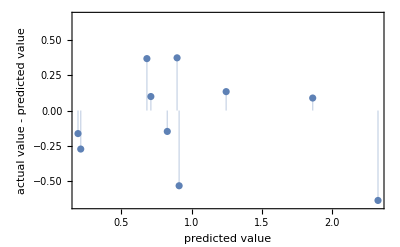
{-Graphics-,0.111908}

```mathematica
pm /@ {"ResidualPlot","MeanSquare"}
```

```mathematica
pm["ComparisonPlot"]
```

pm[ComparisonPlot]

We looked for a pattern in least certain examples. They appear to correspond to ketals.

```mathematica
pm["LeastCertainExamples"]
```

{{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.02383,1.23164,1.02156}→1.29,{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.03177,1.27119,1.04967}→1.11,{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,1.02581,1.28249,1.10122}→1.,{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,0.995367,0.968927,0.969072}→1.05,{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,0.998015,0.99435,0.984067}→0.87,{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.01919,1.22881,1.10965}→0.76,{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.02383,1.23164,1.02156}→0.68,{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,1.00066,0.980226,0.958763}→0.67,{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.02118,1.21751,1.00281}→0.58,{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,1.03508,1.35593,1.08997}→0.41}

## NeuralNetwork

```mathematica
network = NetChain[
{LinearLayer[20],
ElementwiseLayer["Sigmoid"],
LinearLayer[10],
LinearLayer[1]
},
"Input"->12,
"Output"->1
]
```

NetChain[<>]

```mathematica
trainedNetwork=NetTrain[network,Thread[trainingData->Transpose[{trainingResults}]],
ValidationSet->Thread[testData->Transpose[{testResults}]]]
```

NetTrain::invindim: Data provided to port "Input" should be a list of length-12 vectors.

$Failed

```mathematica
predictedTestResults=Map[trainedNetwork,testData]⟦All,1⟧
```

{{1.56584,0.977729,0.965598,0.885357,-0.248082,1.27505,-0.869565,1.,1.02383,1.23164,1.02156},{1.45506,0.996311,0.981894,0.902097,-0.225064,1.36684,-0.881423,1.00141,1.03177,1.27119,1.04967},{0.998319,0.992622,0.976462,0.993575,1.23529,0.480487,1.28854,1.,1.02581,1.28249,1.10122},{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,0.995367,0.968927,0.969072},{1.0554,0.992622,0.996741,0.998985,1.03069,0.964408,0.889328,1.0099,0.998015,0.99435,0.984067},{1.15966,0.959147,0.956183,0.945891,0.800512,0.133313,1.11858,0.992928,1.01919,1.22881,1.10965},{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.02383,1.23164,1.02156},{0.894061,0.962836,0.949303,0.974806,1.33504,0.797065,1.49407,1.00849,1.00066,0.980226,0.958763},{1.62122,0.959147,0.961615,0.883328,-0.225064,1.26975,-0.865613,1.00707,1.02118,1.21751,1.00281},{0.836977,0.985244,0.958356,0.947244,0.790281,0.592882,1.3004,1.00141,1.03508,1.35593,1.08997}}

StandardDeviation:

```mathematica
Sqrt@Mean[(predictedTestResults-testResults)^2]
```

{0.499431,0.284045,0.279717,0.278465,0.791054,0.401524,1.21775,0.304316,0.312586,0.453074,0.326947}

## With Structural Information

## Creating Data

```mathematica
structuraldata=Import["https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/Descriptors%202.xlsx?raw=true","XLSX"];
```

```mathematica
Dimensions@structuraldata
```

{4}

```mathematica
structuraldata=structuraldata[[4,4;;49,4;;]];
```

Part::partd: Part specification structuraldata⟦4,4;;49,4;;All⟧ is longer than depth of object.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of structuraldata⟦4,4;;49,4;;All⟧.

```mathematica
Dimensions@structuraldata
```

{46,16}

```mathematica
structuraldata=Drop[structuraldata,{43}];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of structuraldata⟦4,4;;49,4;;All⟧.

```mathematica
Dimensions@structuraldata
```

{45,16}

```mathematica
(*command to split observations randomly*)
```

```mathematica
trainingIndices=Sort@RandomSample[Range[45],35]
```

{1,2,3,5,6,8,9,10,11,12,13,15,16,17,18,20,22,23,24,25,26,28,29,31,32,33,34,35,36,37,39,40,41,43,45}

```mathematica
fullData=ArrayFlatten[{{inputfinal,structuraldata}}];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of structuraldata⟦4,4;;49,4;;All⟧.

```mathematica
Dimensions[%]
```

{35,27}

```mathematica
trainingData=fullData⟦trainingIndices⟧;
```

Part::partd: Part specification fullData⟦{2,3,5,6,7,8,9,10,11,12,13,15,16,17,18,20,21,22,23,25,26,27,28,29,30,31,32,34,35,36,37,39,40,42,44}⟧ is longer than depth of object.

```mathematica
Dimensions[%]
```

{35,27}

```mathematica
trainingResults=logMU⟦trainingIndices⟧;
```

```mathematica
testIndices=Complement[Range[45],trainingIndices]
```

{4,7,14,19,21,27,30,38,42,44}

```mathematica
testData=fullData⟦testIndices⟧
```

{{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,0.997353,0.957627,0.935333,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.},{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.02449,1.11582,1.2821,0.,1.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.},{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,1.00331,0.997175,0.961575,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.},{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,0.995367,0.968927,0.969072,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,0.994044,0.966102,0.957826,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.03177,1.27119,1.04967,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.},{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.02383,1.23164,1.02156,0.,1.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.},{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.02383,1.23164,1.02156,0.,1.,0.,0.,0.,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,0.998015,0.99435,0.984067,0.,1.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.},{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,1.00066,0.980226,0.958763,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
testResults=logMU⟦testIndices⟧
```

{1.95,1.69,1.27,1.05,1.38,0.81,0.68,0.38,0.03,-0.06}

## Predict

```mathematica
p=Predict[Thread[trainingData->trainingResults],Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,Thread[testData->testResults]];
```

PredictorMeasurements::mlincfttp: Incompatible variable type (Nominal) and variable value ({2.95818,2.77306,2.77439,2.76844,2.68039,2.77335,2.7201,2.77259,2.79103,2.77699,2.78753,3.27407}).

```mathematica
pm /@ {"ResidualPlot","MeanSquare"}
```

{-Graphics-,0.111908}

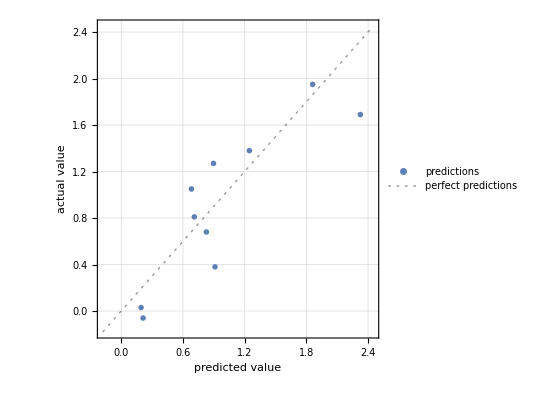

```mathematica
pm["ComparisonPlot"]
```

We looked for a pattern in least certain examples. They appear to correspond to ketals.

```mathematica
pm["LeastCertainExamples"]
```

{{1.06023,0.918705,0.912004,0.895333,0.659847,0.400562,0.498024,1.00283,0.997353,0.957627,0.935333,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.}→1.95,{4.46109,1.00751,1.02969,0.934562,-0.409207,1.02123,0.181818,1.00283,1.02449,1.11582,1.2821,0.,1.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.}→1.69,{0.894055,1.14128,0.931016,0.921711,0.790281,0.505151,0.525692,1.0099,1.00331,0.997175,0.961575,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.}→1.27,{1.11079,0.992622,0.996741,0.999493,1.03836,0.949422,1.04743,1.00849,0.995367,0.968927,0.969072,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.}→1.05,{1.16618,0.944255,0.916712,0.934731,1.18926,1.02279,1.3913,1.00849,0.994044,0.966102,0.957826,1.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.}→1.38,{1.45506,1.,1.00235,0.927968,-0.12532,1.25164,1.1581,0.992928,1.03177,1.27119,1.04967,0.,1.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.}→0.81,{1.56584,0.959147,0.960167,0.88282,-0.209719,1.26225,-0.87747,1.00849,1.02383,1.23164,1.02156,0.,1.,0.,0.,1.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.}→0.68,{1.56584,0.959147,0.950027,0.935577,0.731458,0.952232,1.18577,1.00566,1.02383,1.23164,1.02156,0.,1.,0.,0.,0.,1.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.}→0.38,{1.05539,0.988933,0.992395,0.992898,0.997442,1.01062,0.98419,1.00849,0.998015,0.99435,0.984067,0.,1.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.}→0.03,{0.894052,0.996311,0.985696,0.989009,1.03581,1.14674,1.21739,1.01414,1.00066,0.980226,0.958763,1.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.}→-0.06}

## NeuralNetwork

```mathematica
network = NetChain[
{LinearLayer[20],
ElementwiseLayer["SoftSign"],
LinearLayer[10],
LinearLayer[1]
},
"Input"->27,
"Output"->1
]
```

NetChain[<>]

```mathematica
results=NetTrain[network,Thread[trainingData->Transpose[{trainingResults}]],
ValidationSet->Thread[testData->Transpose[{testResults}]]]
```

NetChain[<>]

```mathematica
Options[trainedNetwork]
```

{<|Type→Chain,Nodes→<|1→<|Type→Linear,Arrays→<|Weights→RawArray[…],Biases→RawArray[…]|>,Parameters→<|OutputDimensions→{20},$OutputSize→20,$InputSize→27,$InputDimensions→{27}|>,Inputs→<|Input→NeuralNetworks`TensorT[{27},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{20},NeuralNetworks`RealT]|>|>,2→<|Type→Elementwise,Arrays→<||>,Parameters→<|Function→NeuralNetworks`ValidatedParameter[NeuralNetworks`Private`ScalarFunctionObject[-Graphics-]],$Dimensions→{20}|>,Inputs→<|Input→NeuralNetworks`TensorT[{20},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{20},NeuralNetworks`RealT]|>|>,3→<|Type→Linear,Arrays→<|Weights→RawArray[…],Biases→RawArray[…]|>,Parameters→<|OutputDimensions→{10},$OutputSize→10,$InputSize→20,$InputDimensions→{20}|>,Inputs→<|Input→NeuralNetworks`TensorT[{20},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{10},NeuralNetworks`RealT]|>|>,4→<|Type→Linear,Arrays→<|Weights→RawArray[…],Biases→RawArray[…]|>,Parameters→<|OutputDimensions→{1},$OutputSize→1,$InputSize→10,$InputDimensions→{10}|>,Inputs→<|Input→NeuralNetworks`TensorT[{10},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{1},NeuralNetworks`RealT]|>|>|>,Edges→{NeuralNetworks`NetPath[Nodes,1,Inputs,Input]→NeuralNetworks`NetPath[Inputs,Input],NeuralNetworks`NetPath[Nodes,2,Inputs,Input]→NeuralNetworks`NetPath[Nodes,1,Outputs,Output],NeuralNetworks`NetPath[Nodes,3,Inputs,Input]→NeuralNetworks`NetPath[Nodes,2,Outputs,Output],NeuralNetworks`NetPath[Nodes,4,Inputs,Input]→NeuralNetworks`NetPath[Nodes,3,Outputs,Output],NeuralNetworks`NetPath[Outputs,Output]→NeuralNetworks`NetPath[Nodes,4,Outputs,Output]},Inputs→<|Input→NeuralNetworks`TensorT[{27},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{1},NeuralNetworks`RealT]|>|>,<|Version→11.3.5|>}

```mathematica
predictedTestResults=Map[trainedNetwork,testData]⟦All,1⟧
```

{1.74521,1.92518,1.44147,0.577786,1.271,0.7047,0.835806,0.246307,0.150166,0.272943}

```mathematica
testResults
```

{1.95,1.69,1.27,1.05,1.38,0.81,0.68,0.38,0.03,-0.06}

StandardDeviation:

```mathematica
Sqrt@Mean[(predictedTestResults-testResults)^2]
```

0.232389

```mathematica
empty={{1,2,3,4},{5,6,7,8},{,,,}}
```

{{1,2,3,4},{5,6,7,8},{Null,Null,Null,Null}}

```mathematica
?DeleteCases
```

DeleteCases[expr,pattern] removes all elements of expr that match pattern. 
DeleteCases[expr,pattern,levelspec] removes all parts of expr on levels specified by levelspec that match pattern. 
DeleteCases[expr,pattern,levelspec,n] removes the first n parts of expr that match pattern. 
DeleteCases[pattern] represents an operator form of DeleteCases that can be applied to an expression.

```mathematica
DeleteCases[empty,{0|Null..},1]
```

{{1,2,3,4},{5,6,7,8}}

```mathematica
DeleteCases[{{1,2,3,4},{5,6,7,8},{Null,Null,Null,Null}},{{0|Null}..},1]
```

{{1,2,3,4},{5,6,7,8},{Null,Null,Null,Null}}

```mathematica
m={{1,2,3,4,0},{2,3,4,5,0},{3,4,5,6,0}}
```

{{1,2,3,4,0},{2,3,4,5,0},{3,4,5,6,0}}

```mathematica
Transpose[m]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{0,0,0}}

```mathematica
DeleteCases[Transpose[m],{0..},1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6}}

```mathematica
DeleteCases[Transpose[m],{Null..}|{0..},1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6}}

```mathematica
DeleteCases[Transpose[{{1,2,3,4,Null},{2,3,4,5,Null},{3,4,5,6,Null}}],{Null..}|{0..},1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6}}

```mathematica
deleteZeroRows[m_]:=DeleteCases[m,{0..}|{Null..},1]
```

```mathematica
deleteZeroRows[{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{Null,Null,Null}}]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6}}

```mathematica
deleteZeroColumns[m_]:=Block[{s},
s=DeleteCases[Transpose[m],{0..}|{Null..},1];
Transpose[s]]
```

```mathematica
deleteZeroColumns[{{1,2,3,4,0},{2,3,4,5,0},{3,4,5,6,0}}]
```

{{1,2,3,4},{2,3,4,5},{3,4,5,6}}

```mathematica
<<DataImportandNormalization`
```

```mathematica
<<SphericalMultivariatePlot`
```

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

```mathematica
Integrate[1/x,x]
```

Log[x]